# Chapter 5: SPI subjected to a in-plane magnetic field

## Author: Bruno Ortega Goes

```mathematica
(*Setting the path where the plots are going to be saved.*)
nbdirectory=SetDirectory[NotebookDirectory[]];
plotsPath =nbdirectory<>"/PlotsChap5/";

Clear[savePlot];
savePlot[nameAndExtension_,plot_,path_:plotsPath]:=If[Length@path ==0,Export[path<>nameAndExtension,plot],  Do[
Export[PlotsPath<>nameAndExtension,plot],{PlotsPath,path}]]
```

## Preamble

```mathematica
overleafDrafpath = "/Users/brunogoes/Dropbox/Aplicativos/Overleaf/00Bruno-Goes-ThesisDraft/Figures/Chap6/";
overleafFinalpath = "/Users/brunogoes/Dropbox/Aplicativos/Overleaf/01Goes-Bruno-PhDThesis/Figures/Chap6/";
overleafNotespath = "/Users/brunogoes/Dropbox/Aplicativos/Overleaf/SPI-Magnetic-field/Figures/Spontaneous-emission/";
pathsList = {plotsPath,overleafDrafpath,overleafFinalpath,overleafNotespath};

(*PlotStyling*)
fontsize = 24;
alphabetlabel={"(a)","(b)","(c)","(d)","(e)","(f)","(g)","(h)","(i)","(j)","(k)","(l)","(m)","(n)","(o)","(p)","(q)","(r)","(s)","(t)","(u)","(v)","(w)","(x)","(y)","(z)"};
ClearAll[MPLColorMap]
<<"http://pastebin.com/raw/pFsb4ZBS";
MPLColorMap["Inferno"];
```

## Parameters set definitions and loading experimental data/simulations☑

```mathematica
(*All the physical parameter are real*)
$Assumptions =
 {nx^2+ny^2+nz^2 == 1 &&
  Ωg>0 &&
  Ωe>0 &&
  ΩR>0 &&
  ΩL>0 &&
 γ>0 &&
 Γ>0};
```

#### 2) Exporting experimental data

It is necessary to change the path of the experimental data in your notebook if you want the program to run!

```mathematica
PrettyTiming[data150=Import["/Users/brunogoes/Dropbox/Research-projects/22--SPIMagneticField/ExperimentalData/Data/Data_150mT.csv"];data250=Import["/Users/brunogoes/Dropbox/Research-projects/22--SPIMagneticField/ExperimentalData/Data/Data_250mT.csv"];data350=Import["/Users/brunogoes/Dropbox/Research-projects/22--SPIMagneticField/ExperimentalData/Data/Data_350mT.csv"];data450=Import["/Users/brunogoes/Dropbox/Research-projects/22--SPIMagneticField/ExperimentalData/Data/Data_450mT.csv"];]
dataexp1list={data150,data250,data350,data450};
```

0h : 0m : 0s

```mathematica
PrettyTiming[data150dcp=Import["/Users/brunogoes/Dropbox/Research-projects/22--SPIMagneticField/ExperimentalData/DataFig2c/Data_150mT_dcp.csv"];data250dcp=Import["/Users/brunogoes/Dropbox/Research-projects/22--SPIMagneticField/ExperimentalData/DataFig2c/Data_250mT_dcp.csv"];data350dcp=Import["/Users/brunogoes/Dropbox/Research-projects/22--SPIMagneticField/ExperimentalData/DataFig2c/Data_350mT_dcp.csv"];data450dcp=Import["/Users/brunogoes/Dropbox/Research-projects/22--SPIMagneticField/ExperimentalData/DataFig2c/Data_450mT_dcp.csv"];]
datadcplist={data150dcp,data250dcp,data350dcp,data450dcp};
```

0h : 0m : 0s

#### 3) Parameters Exp.1: Probing the dynamics and coherence of a semiconductor hole spin via acoustic phonon-assisted excitation

```mathematica
Clear[Experimentalγ,ExperimentalΩe,ExperimentalΩg]
τtrion=450;(*This is constant because it depends solely on the cavity used in the experiment*)

Experimentalγ[τtrion_]:= 1/τtrion;(*ps^-1*)
ExperimentalΩe[B_]:=((0.38*58)/658)B(*ps^-1*);
ExperimentalΩg[B_]:=((0.38*58)/658)B(*ps^-1*);

(*The following experimental physical parameters follow Ref. https://arxiv.org/pdf/2207.05981.pdf*)
PhysicalParameters0   = {Ωe->ExperimentalΩe[0.0]/Experimentalγ[τtrion],Ωg->ExperimentalΩg[0.0]/Experimentalγ[τtrion],γ->1.};
PhysicalParameters30  = {Ωe->ExperimentalΩe[0.03]/Experimentalγ[τtrion],Ωg->ExperimentalΩg[0.03]/Experimentalγ[τtrion],γ->1.};
PhysicalParameters150 = {Ωe->ExperimentalΩe[0.15]/Experimentalγ[τtrion],Ωg->ExperimentalΩg[0.15]/Experimentalγ[τtrion],γ->1.};
PhysicalParameters250 = {Ωe->ExperimentalΩe[0.25]/Experimentalγ[τtrion],Ωg->ExperimentalΩg[0.25]/Experimentalγ[τtrion],γ->1.};
PhysicalParameters350 = {Ωe->ExperimentalΩe[0.35]/Experimentalγ[τtrion],Ωg->ExperimentalΩg[0.35]/Experimentalγ[τtrion],γ->1.};
PhysicalParameters450 = {Ωe->ExperimentalΩe[0.45]/Experimentalγ[τtrion],Ωg->ExperimentalΩg[0.45]/Experimentalγ[τtrion],γ->1.};
PhysicalParameters900= {Ωe->ExperimentalΩe[0.90]/Experimentalγ[τtrion],Ωg->ExperimentalΩg[0.90]/Experimentalγ[τtrion],γ->1.};

PhysicalParameters150 = 
{Ω->ExperimentalΩe[0.15]/Experimentalγ[τtrion],λ->(ExperimentalΩg[0.15]/Experimentalγ[τtrion])/(ExperimentalΩe[0.15]/Experimentalγ[τtrion]),γ->1.};

PhysicalParameters250 = {Ω->ExperimentalΩe[0.25]/Experimentalγ[τtrion],λ->(ExperimentalΩg[0.25]/Experimentalγ[τtrion])/(ExperimentalΩe[0.25]/Experimentalγ[τtrion]),γ->1.};

PhysicalParameters350 = {Ω->ExperimentalΩe[0.35]/Experimentalγ[τtrion],λ->(ExperimentalΩg[0.35]/Experimentalγ[τtrion])/(ExperimentalΩe[0.35]/Experimentalγ[τtrion]),γ->1.};

PhysicalParameters450 = {Ω->ExperimentalΩe[0.45]/Experimentalγ[τtrion],Ωg->(ExperimentalΩg[0.45]/Experimentalγ[τtrion])/(ExperimentalΩe[0.45]/Experimentalγ[τtrion]),γ->1.};

Exp1physicalparameterslist={(*PhysicalParameters0,PhysicalParameters30,*)PhysicalParameters150 ,PhysicalParameters250,PhysicalParameters350,PhysicalParameters450 };

MagneticFieldDirection = {nx->1,ny->0.,nz->0};

texperimentalg2 = 57;
DataTimeRescalingFactorg2 = (2.65/0.48); (*ratio between the maximal points of model and data*)
```

## I. Hilbert space and operators definition☑

In this section I:
	1) Define the Hilbert space structure and the operators, it follows the convention ℋtot = ℋen⊗ℋsp. ;
	2) Obtain the eigenvalues of the density matrix at time t rotated by a general unitary;
	
Defining the subspaces basis:
	For the spin and energy subspaces I have ket0= ketUp = e and ket1= ketDw =g.

```mathematica
ket[0]=ket["upm"]=ket["e"] =Basis[2,1];
ket[1]=ket["dwm"] = ket["g"] =Basis[2,2];
(*I added upm and dwm to emphasize that these are not the physical spin but the mathematucal ones *)
bra[ket_]:=ket*//cf;
```

Defining the basis elements of the spin-energy Hilbert space: ℋtot = ℋen⊗ℋsp.

```mathematica
Do[
ket[i,j]=kron[ket[i],ket[j]],
{i,{"e","g"}},{j,{"upm","dwm"}}
];
```

Defining the operators acting on the total Hilbert space: ℋtot = ℋen⊗ℋsp. 
I use the same notation as in the thesis.

```mathematica
(*Energy subspace operators*) 
(*Remark: Here I added an "E" after σ, so that the σs are the pure Pauli operators always and it makes it explicity that I'm working on the energy subspace.*)
σE   = kron[σm,σ0];
σEx = kron[σx,σ0];
σEy = kron[σy,σ0];
σEz = kron[σz,σ0];

(*Spin subspace operators*)
s=kron[σ0,σm];
sx=kron[σ0,σx];
sy=kron[σ0,σy];
sz=kron[σ0,σz];
```

## II. Rotation operators definition & Coefficients of the wave-function☑

In this section I:
	1) Define the ground and excited state rotation operators

### 1) Definition of the propagators: spontaneous emission, general and simplified☑

```mathematica
(*I'll assume interaction picture with respect to ω0, but I'll carry this factor in all the expressions, in case we want the general expressions containing it, it's just a matter of commenting this line*)
ω0 =0; 
Ce  = ω0 Eye[4]+Ω/2 sx;
Cg=(λ Ω)/2(nx sx + ny sy + nz sz);
```

```mathematica
Clear[ℛg,ℛe]
ℛg[t_]:=MatrixExp[-ⅈ t Cg]//cf;
ℛe[t_]:=MatrixExp[-ⅈ t Ce]//cf;
```

```mathematica
(ℛg[t].ℛg[t]†//cf)==Eye[Length@ℛg[t]]
(ℛe[t]†.ℛe[t]//cf)==Eye[Length@ℛe[t]]
```

True

True

```mathematica
ℛe[t]//mf;
```

(Cos[(t Ω)/2] | -ⅈ Sin[(t Ω)/2] | 0 | 0
-ⅈ Sin[(t Ω)/2] | Cos[(t Ω)/2] | 0 | 0
0 | 0 | Cos[(t Ω)/2] | -ⅈ Sin[(t Ω)/2]
0 | 0 | -ⅈ Sin[(t Ω)/2] | Cos[(t Ω)/2])

```mathematica
ℛg[t]//mf;
```

(Cos[(t λ Ω)/2]-ⅈ nz Sin[(t λ Ω)/2] | (-ⅈ nx-ny) Sin[(t λ Ω)/2] | 0 | 0
(-ⅈ nx+ny) Sin[(t λ Ω)/2] | Cos[(t λ Ω)/2]+ⅈ nz Sin[(t λ Ω)/2] | 0 | 0
0 | 0 | Cos[(t λ Ω)/2]-ⅈ nz Sin[(t λ Ω)/2] | (-ⅈ nx-ny) Sin[(t λ Ω)/2]
0 | 0 | (-ⅈ nx+ny) Sin[(t λ Ω)/2] | Cos[(t λ Ω)/2]+ⅈ nz Sin[(t λ Ω)/2])

```mathematica
aveaRaL[υ_]:= γ Exp[-γ t](ket["e","upm"].ℛe[t].ket["e",υ])*( ket["e","dwm"].ℛe[t].ket["e",υ])
```

```mathematica
( ket["e","dwm"].ℛe[t].ket["e","upm"])
( ket["e","dwm"].ℛe[t].ket["e","dwm"])
```

-ⅈ Sin[(t Ω)/2]

Cos[(t Ω)/2]

```mathematica
(ket["e","upm"].ℛe[t].ket["e","upm"])
(ket["e","upm"].ℛe[t].ket["e","dwm"])
```

Cos[(t Ω)/2]

-ⅈ Sin[(t Ω)/2]

```mathematica
Clear[𝕄0,𝕌0,𝕄,𝕌](*ne->-ⅈ γ/2*)
(*Matrices without drive: Spontaneous emission case*)
𝕄0=(Ce.σE†.σE - Cg.σE.σE†)+ne σE†.σE//mf;(*ne is just a dummy variable, this is related to the 'bug' explained in the appendix*)
𝕌0[t_]:=MatrixExp[-ⅈ t 𝕄0]/.ne->-ⅈ γ/2//cf;
𝕌0::usage = "Takes the evolution time t as an argument. The internal parameters of this function that must be defined are: the Larmor frequencies Ωe and Ωg, the drirection of the magnetic field in the ground state (nx,ny,nz), the decay rate γ (usually taken to be 1).";

(*Matrices with drive*)
𝕄=(Ce.σE†.σE - Cg.σE.σE†)+(ΩL/2 s.s†+ΩR/2 s†.s).σEy +ne σE†.σE//mf;
𝕌[t_]:=MatrixExp[-ⅈ t 𝕄]/.ne->(-ⅈ γ/2);
𝕌::usage = "Takes the evolution time t as an argument. The internal parameters of this function that must be defined are: the Larmor frequencies Ωe and Ωg, the drirection of the magnetic field in the ground state (nx,ny,nz), the decay rate γ (usually taken to be 1) and the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";

(*Matrices with drive neglecting Overhauser*)
𝕄mod=𝕄/.λ->1/.ΩR->ΩH/.ΩL->ΩH/.nx->1/.ny->0/.nz->0//cf//mf;
𝕌mod[s_]:=MatrixExp[- ⅈ s 𝕄mod]/.ne->-ⅈ γ/2;
```

(ne | Ω/2 | 0 | 0
Ω/2 | ne | 0 | 0
0 | 0 | -1/2 nz λ Ω | -1/2 (nx-ⅈ ny) λ Ω
0 | 0 | -1/2 (nx+ⅈ ny) λ Ω | (nz λ Ω)/2)

(ne | Ω/2 | -(ⅈ ΩR)/2 | 0
Ω/2 | ne | 0 | -(ⅈ ΩL)/2
(ⅈ ΩR)/2 | 0 | -1/2 nz λ Ω | -1/2 (nx-ⅈ ny) λ Ω
0 | (ⅈ ΩL)/2 | -1/2 (nx+ⅈ ny) λ Ω | (nz λ Ω)/2)

(ne | Ω/2 | -(ⅈ ΩH)/2 | 0
Ω/2 | ne | 0 | -(ⅈ ΩH)/2
(ⅈ ΩH)/2 | 0 | 0 | -Ω/2
0 | (ⅈ ΩH)/2 | -Ω/2 | 0)

### 2) Coefficients for spontaneous emission☑

```mathematica
Clear[f0SE];
f0SE[finalenergy_,finalspin_, initialenergy_,initialspin_,t_]:=ket[finalenergy,finalspin].𝕌0[t].ket[initialenergy,initialspin]
f0SE::usage = "The order of the arguments is: the system final state: energy and spin, the system initial state: energy and spin, and the time variable t. The internal parameters of this function that must be defined are: the Larmor frequencies Ωe and Ωg, the drirection of the magnetic field in the ground state (nx,ny,nz), the decay rate γ (by default 1) and the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";
```

```mathematica
Clear[f1RSE];
f1RSE[finalenergy_,finalspin_, initialenergy_,initialspin_,t_,t1_,γ_:1]:=√γ(ket[finalenergy,finalspin].𝕌0[t-t1].ket["g","upm"])(ket["e","upm"].𝕌0[t1].ket[initialenergy,initialspin])
f1RSE::usage = "The order of the arguments is: the system final state: energy and spin, the system initial state: energy and spin, the time variable t, and the time of photon emission event t1. The internal parameters of this function that must be defined are: the Larmor frequencies Ωe and Ωg, the drirection of the magnetic field in the ground state (nx,ny,nz), the decay rate γ (default 1) and the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";
```

```mathematica
Clear[f1LSE];
f1LSE[finalenergy_,finalspin_, initialenergy_,initialspin_,t_,t1_,γ_:1]:=√γ(ket[finalenergy,finalspin].𝕌0[t-t1].ket["g","dwm"])(ket["e","dwm"].𝕌0[t1].ket[initialenergy,initialspin])
f1LSE::usage = "The order of the arguments is: the system final state: energy and spin, the system initial state: energy and spin, the time variable t, and the time of photon emission event t1. The internal parameters of this function that must be defined are: the Larmor frequencies Ωe and Ωg, the drirection of the magnetic field in the ground state (nx,ny,nz), the decay rate γ (usually taken to be 1) and the drive amplitudes ΩL and ΩR. For ΩL=ΩR=0, i.e. in the absence of a drive, we obtain 𝕌0, the spontaneous emission case.";
```

```mathematica
(*Spontaneous emission case coefficients*)
TextGrid[
{{"Intial Spin","f0e↑","f0e↓","f1Rg↑","f1Rg↓","f1Lg↑","f1Rg↓"},

{"↑",
f0SE["e","upm","e", "upm",t],
f0SE["e","dwm","e","upm",t],
f1RSE["g","upm","e","upm",t,t1],
f1RSE["g","dwm","e","upm",t,t1],
f1LSE["g","upm","e","upm",t,t1],
f1LSE["g","dwm","e","upm",t,t1]},


{"↓",
f0SE["e","upm","e", "dwm",t],
f0SE["e","dwm","e","dwm",t],
f1RSE["g","upm","e","dwm",t,t1],
f1RSE["g","dwm","e","dwm",t,t1],
f1LSE["g","upm","e","dwm",t,t1],
f1LSE["g","dwm","e","dwm",t,t1]}},

Frame->All]
```

Intial Spin | f0e↑ | f0e↓ | f1Rg↑ | f1Rg↓ | f1Lg↑ | f1Rg↓
↑ | ⅇ^(-(t γ)/2) Cos[(t Ω)/2] | -ⅈ ⅇ^(-(t γ)/2) Sin[(t Ω)/2] | ⅇ^(-(t1 γ)/2) Cos[(t1 Ω)/2] (Cos[1/2 (t-t1) λ Ω]+ⅈ nz Sin[1/2 (t-t1) λ Ω]) | ⅈ ⅇ^(-(t1 γ)/2) (nx+ⅈ ny) Cos[(t1 Ω)/2] Sin[1/2 (t-t1) λ Ω] | -ⅈ ⅇ^(-(t1 γ)/2) (ⅈ nx+ny) Sin[(t1 Ω)/2] Sin[1/2 (t-t1) λ Ω] | -ⅈ ⅇ^(-(t1 γ)/2) Sin[(t1 Ω)/2] (Cos[1/2 (t-t1) λ Ω]-ⅈ nz Sin[1/2 (t-t1) λ Ω])
↓ | -ⅈ ⅇ^(-(t γ)/2) Sin[(t Ω)/2] | ⅇ^(-(t γ)/2) Cos[(t Ω)/2] | -ⅈ ⅇ^(-(t1 γ)/2) Sin[(t1 Ω)/2] (Cos[1/2 (t-t1) λ Ω]+ⅈ nz Sin[1/2 (t-t1) λ Ω]) | ⅇ^(-(t1 γ)/2) (nx+ⅈ ny) Sin[(t1 Ω)/2] Sin[1/2 (t-t1) λ Ω] | ⅇ^(-(t1 γ)/2) (ⅈ nx+ny) Cos[(t1 Ω)/2] Sin[1/2 (t-t1) λ Ω] | ⅇ^(-(t1 γ)/2) Cos[(t1 Ω)/2] (Cos[1/2 (t-t1) λ Ω]-ⅈ nz Sin[1/2 (t-t1) λ Ω])

Computing the probabilities for the spontaneous emission: Assuming the spin is initially ↑

```mathematica
Clear[P0SE,P1RSE,P1LSE];
Module[{ampR,ampL, initialspin},
initialspin="upm";
PrettyTiming@Do[
(*Amplitude of no-photon emission squared*)
P0SE[ϵf,sf,"e",initialspin,t]=f0SE[ϵf,sf,"e",initialspin,t]f0SE[ϵf,sf,"e", initialspin,t]*;

(*Amplitude of R-photon emission squared and integrate over all t1*)
ampR=f1RSE[ϵf,sf,"e",initialspin,t,t1]f1RSE[ϵf,sf,"e",initialspin,t,t1]*//cf;
P1RSE[ϵf,sf,"e",initialspin,t]=Integrate[ampR,{t1,0,t}];

(*Amplitude of L-photon emission squared and integrate over all t1*)
ampL=f1LSE[ϵf,sf,"e",initialspin,t,t1]f1LSE[ϵf,sf,"e",initialspin,t,t1]*//cf;
P1LSE[ϵf,sf,"e","upm",t]=Integrate[ampL,{t1,0,t}],

{ϵf,{"e","g"}},{sf,{"upm","dwm"}}

]
]
```

0h : 2m : 16s

Sanity check: Is the wave-function properly normalized?

```mathematica
Sum[P0SE[ϵf,sf,"e","upm",t]+P1RSE[ϵf,sf,"e","upm",t]+P1LSE[ϵf,sf,"e","upm",t],{ϵf,{"e","g"}},{sf,{"upm","dwm"}}]//cf
```

1

Yes!

## III.Model validation☑

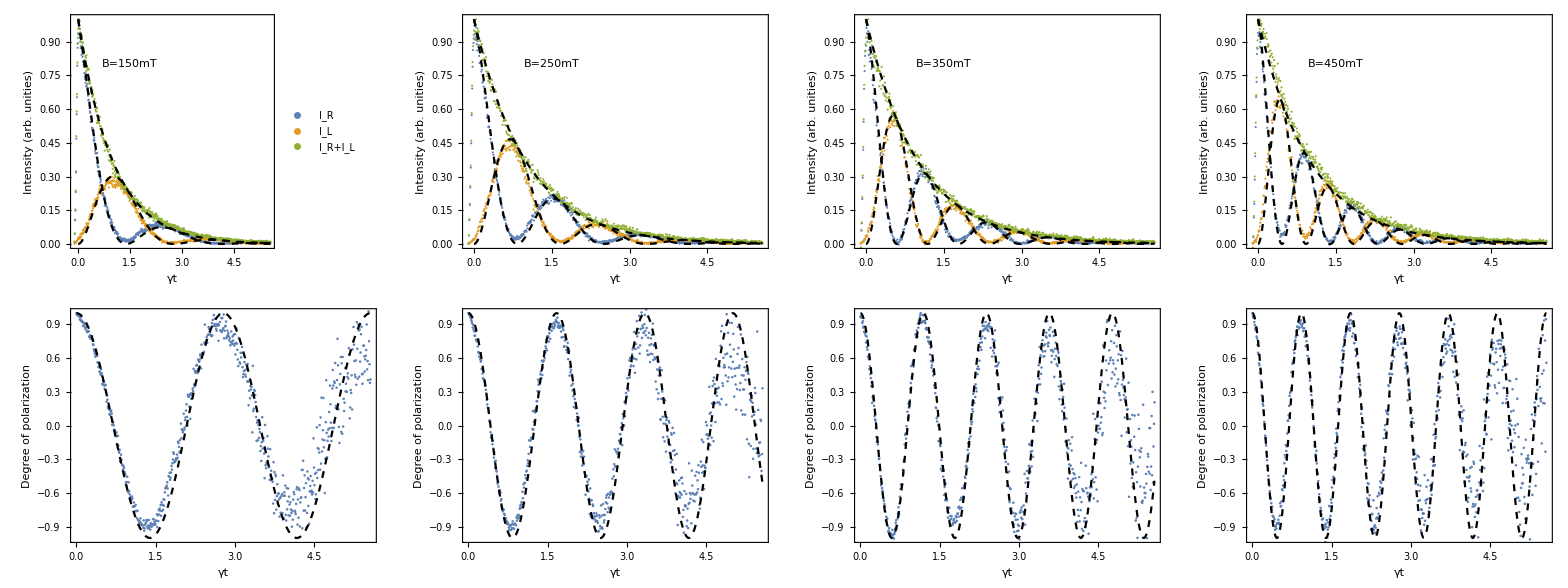

```mathematica
Clear[DCP];
texperimental = 5.56;(*Used to keep γ=1*)
(*Degre of circular polarization*)
DCP=(IRUpSE-ILUpSE)/(IRUpSE+ILUpSE)//cf;

Module[{timescaling,dataset1,dataset2,physicalparameters,epilog},
timescaling =5.56/2.5 (*Used to keep γ=1*);
dataset1=dataexp1list;
dataset2=datadcplist;
epilog={"B=150mT","B=250mT","B=350mT","B=450mT"};
physicalparameters=Exp1physicalparameterslist;
modelValidation=Grid[{
(*First row*)
Table[
Show[
ListPlot[{
Table[{dataset1[[k]]⟦i,1⟧*timescaling, dataset1[[k]]⟦i,2⟧},{i,1,Length@dataset1[[k]]}],Table[{dataset1[[k]]⟦i,1⟧*timescaling,dataset1[[k]]⟦i,3⟧},{i,1,Length@dataset1[[k]]}],Table[{dataset1[[k]]⟦i,1⟧*timescaling, dataset1[[k]]⟦i,4⟧},{i,1,Length@dataset1[[k]]}]},
PlotRange->{All,{0,1}},
PlotLegends->If[k==1,legend[{"I_R","I_L" ,"I_R+I_L"},{0.8,0.7}],None],
FrameLabel->{"γt","Intensity (arb. unities)"},
Epilog->Inset[Framed[Style[epilog[[k]]],Background->LightYellow],{1.5,0.8}]],

Plot[{IRUpSE/.physicalparameters[[k]],
ILUpSE/.physicalparameters[[k]],
IRUpSE+ILUpSE/.physicalparameters[[k]]},
{t,0,texperimental},

PlotStyle->{{Black,Dashed},{Black,Dashed},{Black,Dashed}},
PlotRange->{All,{0,1}},
PlotLegends->legend[{"I_R","I_L" ,"I_R+I_L"},{0.8,0.7}],
FrameLabel->{"γt","Intensity (arb. unities)"},
Epilog->Inset[Framed[Style[k],Background->LightYellow],{1.5,0.8}]]
],
{k,1,Length@dataset1}],

(*Second row*)
Table[
Show[
ListPlot[
Table[{dataset2[[k]]⟦i,1⟧*(5.56/2.5),
           dataset2[[k]]⟦i,2⟧},{i,1,Length@dataset2[[k]]}],
PlotRange->{All,{-1,1}},
FrameLabel->{"γt","Degree of polarization"}],

Plot[DCP/.physicalparameters[[k]],{t,0,texperimental},
PlotStyle->{{Black, Dashed}},
PlotRange->{All,{-1,1}},
FrameLabel->{"γt","Degree of polarization"}]],
{k,1,Length@dataset2}
]
}]
]
savePlot["modelValidation-ExperimentalDatavsModel.pdf", modelValidation];
```

## IV. Fidelity of the spin at the moment of re-excitation☑

### 1) Spin state at time t: Analytical calculations ☑

Ideal protocol parameters:

```mathematica
idealprotocolparamaters = {γ->1,nx->1,ny->0,nz->0,λ->1};
idealalignementparamaters = {γ->1,nx->1,ny->0,nz->0};(*λ can change*)
```

```mathematica
<<overlapsforSpinState.mx
```

In this section I:
	1) Perform the integrals to obtain the matrix elements of the spin density matrix analytically;
	2) Obtain the eigenvalues of the density matrix at time t rotated by a general unitary;

Mathematica has some problem with understanding that some parameters are real, so when we conjugate something it considers everything as a complex number. That’s why I write all the expressions explicitly and use the cf command (from Melt!) to FullSimplify considering the parameters real. If I don’t do this, Mathematica simply doesn’t perform the necessary integrals.

Below I compute all the overlaps for all times, that’s to say, I’m not simplifying to the long time limit, so all the expressions below DO HAVE the excited state component.

#### a) Computing the overlaps

```mathematica
PrettyTiming[
Module[{FirstTerm, SecondTerm,ThirdTerm,Product1,Product2,FirstIntegral,SecondIntegral},

FirstTerm=Exp[-γ t] (ket["e", "upm"]*.ℛe[t].ket["e", "upm"])*ket["e", "upm"]*.ℛe[t].ket["e", "upm"] //cf;(*✓*)

SecondTerm=(ket["g", "upm"]*.ℛg[t-u].ket["g", "upm"])*ket["g", "upm"]*.ℛg[t-u].ket["g", "upm"]//cf;(*✓*)
Product1=f0SE["e","upm","e","upm",u]*f0SE["e","upm","e","upm",u]//cf;(*✓*)

ThirdTerm=(ket["g", "upm"]*.ℛg[t-u].ket["g", "dwm"])*ket["g", "upm"]*.ℛg[t-u].ket["g", "dwm"]//cf;(*✓*)
Product2=f0SE["e","dwm","e","upm",u]*f0SE["e","dwm","e","upm",u]//cf;(*✓*)

PrettyTiming[FirstIntegral=Integrate[SecondTerm Product1//cf,{u,0,t}]];
PrettyTiming[SecondIntegral= Integrate[ThirdTerm Product2//cf,{u,0,t}]];

ℴUpUp = FirstTerm +γ(FirstIntegral+SecondIntegral)/.(nx^2+ny^2)->1-nz^2//cf(*✓*);
ℴUpUpg = γ(FirstIntegral+SecondIntegral)/.(nx^2+ny^2)->1-nz^2//cf(*✓*);
]
]
```

0h : 0m : 26s

0h : 0m : 39s

0h : 6m : 12s

```mathematica
ℴUpUp
```

1/4 (2+(ⅇ^(ⅈ t λ Ω) (-1+nz^2) γ (-ⅈ γ+λ Ω))/((ⅈ γ+Ω-λ Ω) (γ+ⅈ (1+λ) Ω))+(2 nz^2 γ^2)/(γ^2+Ω^2)-(ⅇ^(-ⅈ t λ Ω) (-1+nz^2) γ (γ-ⅈ λ Ω))/(γ^2-2 ⅈ γ λ Ω+Ω^2-λ^2 Ω^2)+(ⅇ^(-t (γ-ⅈ Ω)) γ (-γ^2+2 ⅈ γ Ω+Ω^2-nz^2 λ^2 Ω^2))/((γ-ⅈ Ω) (γ^2-2 ⅈ γ Ω+(-1+λ^2) Ω^2))-(ⅇ^(-t (γ+ⅈ Ω)) γ (γ^2+2 ⅈ γ Ω+(-1+nz^2 λ^2) Ω^2))/((γ+ⅈ Ω) (γ^2+2 ⅈ γ Ω+(-1+λ^2) Ω^2))+2 ⅇ^(-t γ) Cos[t Ω])

```mathematica
ℴUpUpg
```

1/8 (4-4 ⅇ^(-t γ)+(2 ⅇ^(ⅈ t λ Ω) (-1+nz^2) γ (-ⅈ γ+λ Ω))/((ⅈ γ+Ω-λ Ω) (γ+ⅈ (1+λ) Ω))+(4 nz^2 γ^2)/(γ^2+Ω^2)-(2 ⅇ^(-ⅈ t λ Ω) (-1+nz^2) γ (γ-ⅈ λ Ω))/(γ^2-2 ⅈ γ λ Ω-(-1+λ^2) Ω^2)-(2 ⅇ^(-t (γ-ⅈ Ω)) γ (γ^2-2 ⅈ γ Ω+(-1+nz^2 λ^2) Ω^2))/((γ-ⅈ Ω) (γ^2-2 ⅈ γ Ω+(-1+λ^2) Ω^2))-(2 ⅇ^(-t (γ+ⅈ Ω)) γ (γ^2+2 ⅈ γ Ω+(-1+nz^2 λ^2) Ω^2))/((γ+ⅈ Ω) (γ^2+2 ⅈ γ Ω+(-1+λ^2) Ω^2)))

```mathematica
PrettyTiming[
Module[{FirstTerm, SecondTerm,ThirdTerm,Product1,Product2,FirstIntegral,SecondIntegral},

FirstTerm=Exp[-γ t] (ket["e", "dwm"]*.ℛe[t].ket["e", "upm"])*ket["e", "dwm"]*.ℛe[t].ket["e", "upm"]//cf;(*✓*)

SecondTerm=(ket["g","dwm"]*.ℛg[t-u].ket["g", "upm"])*ket["g", "dwm"]*.ℛg[t-u].ket["g", "upm"]//cf;(*✓*)
Product1=f0SE["e","upm","e","upm",u]*f0SE["e","upm","e","upm",u]//cf;(*✓*)

ThirdTerm=(ket["g", "dwm"]*.ℛg[t-u].ket["g", "dwm"])*ket["g", "dwm"]*.ℛg[t-u].ket["g", "dwm"]//cf;(*✓*)
Product2=f0SE["e","dwm","e","upm",u]*f0SE["e","dwm","e","upm",u]//cf;(*✓*)
FirstIntegral = Integrate[(SecondTerm Product1)//cf,{u,0,t}];
SecondIntegral = Integrate[(ThirdTerm Product2)//cf,{u,0,t}];

ℴDwDw = FirstTerm +γ(FirstIntegral+SecondIntegral)/.(nx^2+ny^2)->1-nz^2//cf(*✓*);

ℴDwDwg =γ(FirstIntegral+SecondIntegral)/.(nx^2+ny^2)->1-nz^2//cf(*✓*);
]
]
```

0h : 7m : 5s

```mathematica
ℴDwDw
```

1/8 (4-(4 nz^2 γ^2)/(γ^2+Ω^2)-4 ⅇ^(-t γ) Cos[t Ω]+(4 ⅇ^(-t γ) γ (γ (γ^4+γ^2 (2+(1+nz^2) λ^2) Ω^2+(1+λ^2+nz^2 λ^2 (-3+λ^2)) Ω^4) Cos[t Ω]-Ω (γ^4+γ^2 (2+(-1+3 nz^2) λ^2) Ω^2+(-1+λ^2) (-1+nz^2 λ^2) Ω^4) Sin[t Ω]+ⅇ^(t γ) (-1+nz^2) (γ^2+Ω^2) (γ (γ^2+(1+λ^2) Ω^2) Cos[t λ Ω]+λ Ω (γ^2+(-1+λ^2) Ω^2) Sin[t λ Ω])))/((γ^2+Ω^2) (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2)))

```mathematica
ℴDwDwg
```

1/4 (2-2 ⅇ^(-t γ)-(2 nz^2 γ^2)/(γ^2+Ω^2)+(ⅇ^(-ⅈ t λ Ω) (-1+nz^2) γ (γ-ⅈ λ Ω))/(γ^2-2 ⅈ γ λ Ω-(-1+λ^2) Ω^2)+(ⅈ ⅇ^(ⅈ t λ Ω) (-1+nz^2) γ (-ⅈ γ+λ Ω))/(γ^2+2 ⅈ γ λ Ω-(-1+λ^2) Ω^2)+(ⅇ^(-t (γ-ⅈ Ω)) γ (γ^2-2 ⅈ γ Ω+(-1+nz^2 λ^2) Ω^2))/((γ-ⅈ Ω) (γ^2-2 ⅈ γ Ω+(-1+λ^2) Ω^2))+(ⅇ^(-t (γ+ⅈ Ω)) γ (γ^2+2 ⅈ γ Ω+(-1+nz^2 λ^2) Ω^2))/((γ+ⅈ Ω) (γ^2+2 ⅈ γ Ω+(-1+λ^2) Ω^2)))

```mathematica
PrettyTiming[

Module[{FirstTerm, SecondTerm,ThirdTerm,Product1,Product2, FirstIntegral,SecondIntegral},

FirstTerm=Exp[-γ t](ket["e", "dwm"]*.ℛe[t].ket["e", "upm"])*ket["e", "upm"]*.ℛe[t].ket["e", "upm"]//cf;(*✓*)

SecondTerm=(ket["g", "dwm"]*.ℛg[t-u].ket["g", "upm"])*ket["g", "upm"]*.ℛg[t-u].ket["g", "upm"]//cf;
Product1=f0SE["e","upm","e","upm",u]*f0SE["e","upm","e","upm",u]//cf;(*✓*)

ThirdTerm=(ket["g", "dwm"]*.ℛg[t-u].ket["g", "dwm"])* ket["g", "upm"]*.ℛg[t-u].ket["g", "dwm"]//cf;(*✓-There was a correction here! The not conjugated part was swaped the Up and Dw*)
Product2=f0SE["e","dwm","e","upm",u]*f0SE["e","dwm","e","upm",u]//cf;(*✓*)

FirstIntegral = Integrate[(SecondTerm Product1)//cf,{u,0,t}];
SecondIntegral = Integrate[(ThirdTerm Product2)//cf,{u,0,t}];

ℴDwUp = FirstTerm+γ(FirstIntegral+SecondIntegral)//cf;

ℴDwUpg = γ(FirstIntegral+SecondIntegral)//cf;

]
]
```

0h : 10m : 43s

```mathematica
ℴDwUp
```

1/4 (2 ⅈ ⅇ^(-t γ) Sin[t Ω]-(2 (nx-ⅈ ny) γ (nz γ (-γ^4-2 γ^2 (1+λ^2) Ω^2-(-1+λ^2)^2 Ω^4)+(γ^2+Ω^2) (ⅈ λ Ω (γ^2+(-1+λ^2) Ω^2)+nz γ (γ^2+(1+λ^2) Ω^2)) Cos[t λ Ω]+ⅇ^(-t γ) λ Ω ((-ⅈ γ^4+nz γ^3 λ Ω-ⅈ γ^2 λ^2 Ω^2+nz γ λ (-3+λ^2) Ω^3-ⅈ (-1+λ^2) Ω^4) Cos[t Ω]+Ω (2 ⅈ γ^3-3 nz γ^2 λ Ω+2 ⅈ γ Ω^2-nz λ (-1+λ^2) Ω^3) Sin[t Ω])+(γ^2+Ω^2) (-ⅈ γ^3+nz γ^2 λ Ω-ⅈ γ (1+λ^2) Ω^2+nz λ (-1+λ^2) Ω^3) Sin[t λ Ω]))/(γ^6+γ^4 (3+2 λ^2) Ω^2+γ^2 (3+λ^4) Ω^4+(-1+λ^2)^2 Ω^6))

```mathematica
ℴDwUpg
```

-((ⅇ^(-2 t γ+ⅈ t (-1+λ) Ω) (nx-ⅈ ny) γ (ⅇ^(2 t γ+ⅈ t Ω) (-1+nz) (γ-ⅈ Ω) (γ+ⅈ Ω) (γ-ⅈ (-1+λ) Ω) (γ+ⅈ λ Ω) (γ-ⅈ (1+λ) Ω)+ⅇ^(t (2 γ+ⅈ (1-2 λ) Ω)) (1+nz) (γ-ⅈ Ω) (γ+ⅈ Ω) (γ+ⅈ (-1+λ) Ω) (γ-ⅈ λ Ω) (γ+ⅈ (1+λ) Ω)-2 ⅇ^(t (2 γ-ⅈ (-1+λ) Ω)) nz γ (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2)+ⅇ^(t (γ-ⅈ λ Ω)) λ (γ-ⅈ Ω) Ω (-ⅈ γ+Ω+nz λ Ω) (γ^2-2 ⅈ γ Ω+(-1+λ^2) Ω^2)+ⅇ^(t (γ-ⅈ (-2+λ) Ω)) λ (γ+ⅈ Ω) Ω (-ⅈ γ+(-1+nz λ) Ω) (γ^2+2 ⅈ γ Ω+(-1+λ^2) Ω^2)))/(4 (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4)))

```mathematica
ℴUpDw=Conjugate[ℴDwUp]
```

1/4 Conjugate[2 ⅈ ⅇ^(-t γ) Sin[t Ω]-(2 (nx-ⅈ ny) γ (nz γ (-γ^4-2 γ^2 (1+λ^2) Ω^2-(-1+λ^2)^2 Ω^4)+(γ^2+Ω^2) (ⅈ λ Ω (γ^2+(-1+λ^2) Ω^2)+nz γ (γ^2+(1+λ^2) Ω^2)) Cos[t λ Ω]+ⅇ^(-t γ) λ Ω ((-ⅈ γ^4+nz γ^3 λ Ω-ⅈ γ^2 λ^2 Ω^2+nz γ λ (-3+λ^2) Ω^3-ⅈ (-1+λ^2) Ω^4) Cos[t Ω]+Ω (2 ⅈ γ^3-3 nz γ^2 λ Ω+2 ⅈ γ Ω^2-nz λ (-1+λ^2) Ω^3) Sin[t Ω])+(γ^2+Ω^2) (-ⅈ γ^3+nz γ^2 λ Ω-ⅈ γ (1+λ^2) Ω^2+nz λ (-1+λ^2) Ω^3) Sin[t λ Ω]))/(γ^6+γ^4 (3+2 λ^2) Ω^2+γ^2 (3+λ^4) Ω^4+(-1+λ^2)^2 Ω^6)]

Yeah, Mathematica doesn’t conjugate smartly. We have to outsmart Mathematica, below I do it by hand:

```mathematica
ℴUpDw=1/4 (-2 ⅈ ⅇ^(-t γ) Sin[t Ω]-(2 (nx+ⅈ ny) γ (nz γ (-γ^4-2 γ^2 (1+λ^2) Ω^2-(-1+λ^2)^2 Ω^4)+(γ^2+Ω^2) (-ⅈ λ Ω (γ^2+(-1+λ^2) Ω^2)+nz γ (γ^2+(1+λ^2) Ω^2)) Cos[t λ Ω]+ⅇ^(-t γ) λ Ω ((ⅈ γ^4+nz γ^3 λ Ω+ⅈ γ^2 λ^2 Ω^2+nz γ λ (-3+λ^2) Ω^3+ⅈ (-1+λ^2) Ω^4) Cos[t Ω]+Ω (-2 ⅈ γ^3-3 nz γ^2 λ Ω-2 ⅈ γ Ω^2-nz λ (-1+λ^2) Ω^3) Sin[t Ω])+(γ^2+Ω^2) (ⅈ γ^3+nz γ^2 λ Ω+ⅈ γ (1+λ^2) Ω^2+nz λ (-1+λ^2) Ω^3) Sin[t λ Ω]))/(γ^6+γ^4 (3+2 λ^2) Ω^2+γ^2 (3+λ^4) Ω^4+(-1+λ^2)^2 Ω^6))
```

1/4 (-2 ⅈ ⅇ^(-t γ) Sin[t Ω]-(2 (nx+ⅈ ny) γ (nz γ (-γ^4-2 γ^2 (1+λ^2) Ω^2-(-1+λ^2)^2 Ω^4)+(γ^2+Ω^2) (-ⅈ λ Ω (γ^2+(-1+λ^2) Ω^2)+nz γ (γ^2+(1+λ^2) Ω^2)) Cos[t λ Ω]+ⅇ^(-t γ) λ Ω ((ⅈ γ^4+nz γ^3 λ Ω+ⅈ γ^2 λ^2 Ω^2+nz γ λ (-3+λ^2) Ω^3+ⅈ (-1+λ^2) Ω^4) Cos[t Ω]+Ω (-2 ⅈ γ^3-3 nz γ^2 λ Ω-2 ⅈ γ Ω^2-nz λ (-1+λ^2) Ω^3) Sin[t Ω])+(γ^2+Ω^2) (ⅈ γ^3+nz γ^2 λ Ω+ⅈ γ (1+λ^2) Ω^2+nz λ (-1+λ^2) Ω^3) Sin[t λ Ω]))/(γ^6+γ^4 (3+2 λ^2) Ω^2+γ^2 (3+λ^4) Ω^4+(-1+λ^2)^2 Ω^6))

```mathematica
ℴUpDwg=-((ⅇ^(-2 t γ-ⅈ t (-1+λ) Ω) (nx+ⅈ ny) γ (ⅇ^(2 t γ-ⅈ t Ω) (-1+nz) (γ+ⅈ Ω) (γ-ⅈ Ω) (γ+ⅈ (-1+λ) Ω) (γ-ⅈ λ Ω) (γ+ⅈ (1+λ) Ω)+ⅇ^(t (2 γ-ⅈ (1-2 λ) Ω)) (1+nz) (γ+ⅈ Ω) (γ-ⅈ Ω) (γ-ⅈ (-1+λ) Ω) (γ+ⅈ λ Ω) (γ-ⅈ (1+λ) Ω)-2 ⅇ^(t (2 γ+ⅈ (-1+λ) Ω)) nz γ (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2)+ⅇ^(t (γ+ⅈ λ Ω)) λ (γ+ⅈ Ω) Ω (ⅈ γ+Ω+nz λ Ω) (γ^2+2 ⅈ γ Ω+(-1+λ^2) Ω^2)+ⅇ^(t (γ+ⅈ (-2+λ) Ω)) λ (γ-ⅈ Ω) Ω (ⅈ γ+(-1+nz λ) Ω) (γ^2-2 ⅈ γ Ω+(-1+λ^2) Ω^2)))/(4 (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4)))
```

-((ⅇ^(-2 t γ-ⅈ t (-1+λ) Ω) (nx+ⅈ ny) γ (ⅇ^(t (2 γ-ⅈ (1-2 λ) Ω)) (1+nz) (γ-ⅈ Ω) (γ+ⅈ Ω) (γ-ⅈ (-1+λ) Ω) (γ+ⅈ λ Ω) (γ-ⅈ (1+λ) Ω)+ⅇ^(2 t γ-ⅈ t Ω) (-1+nz) (γ-ⅈ Ω) (γ+ⅈ Ω) (γ+ⅈ (-1+λ) Ω) (γ-ⅈ λ Ω) (γ+ⅈ (1+λ) Ω)-2 ⅇ^(t (2 γ+ⅈ (-1+λ) Ω)) nz γ (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2)+ⅇ^(t (γ+ⅈ (-2+λ) Ω)) λ (γ-ⅈ Ω) Ω (ⅈ γ+(-1+nz λ) Ω) (γ^2-2 ⅈ γ Ω+(-1+λ^2) Ω^2)+ⅇ^(t (γ+ⅈ λ Ω)) λ (γ+ⅈ Ω) Ω (ⅈ γ+Ω+nz λ Ω) (γ^2+2 ⅈ γ Ω+(-1+λ^2) Ω^2)))/(4 (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4)))

As it takes a lot of time to compute these overlaps I’ll save them:

```mathematica
DumpSave["overlapsforSpinState.mx",{ℴUpUp,ℴDwDw,ℴDwUp,ℴUpDw,ℴUpUpg,ℴDwDwg,ℴDwUpg,ℴUpDwg}];
```

#### b) Density matrix and fidelity: general analytics

```mathematica
<<AnalyticalExpressionOfTheFidelity.mx
```

The density matrix for the mathematical spin, i.e., the one considering the decay as well, is given by:

```mathematica
ρmathematicalspin =({{ℴUpUp, ℴDwUp}, {ℴUpDw, ℴDwDw}})//mf;
```

(1/4 (2+(ⅇ^(ⅈ t λ Ω) (-1+nz^2) γ (-ⅈ γ+λ Ω))/((ⅈ γ+Ω-λ Ω) (γ+ⅈ (1+λ) Ω))+(2 nz^2 γ^2)/(γ^2+Ω^2)-(ⅇ^(-ⅈ t λ Ω) (-1+nz^2) γ (γ-ⅈ λ Ω))/(γ^2-2 ⅈ γ λ Ω+Ω^2-λ^2 Ω^2)+(ⅇ^(-t (γ-ⅈ Ω)) γ (-γ^2+2 ⅈ γ Ω+Ω^2-nz^2 λ^2 Ω^2))/((γ-ⅈ Ω) (γ^2-2 ⅈ γ Ω+(-1+λ^2) Ω^2))-(ⅇ^(-t (γ+ⅈ Ω)) γ (γ^2+2 ⅈ γ Ω+(-1+nz^2 λ^2) Ω^2))/((γ+ⅈ Ω) (γ^2+2 ⅈ γ Ω+(-1+λ^2) Ω^2))+2 ⅇ^(-t γ) Cos[t Ω]) | 1/4 (2 ⅈ ⅇ^(-t γ) Sin[t Ω]-(2 (nx-ⅈ ny) γ (nz γ (-γ^4-2 γ^2 (1+λ^2) Ω^2-(-1+λ^2)^2 Ω^4)+(γ^2+Ω^2) (ⅈ λ Ω (γ^2+(-1+λ^2) Ω^2)+nz γ (γ^2+(1+λ^2) Ω^2)) Cos[t λ Ω]+ⅇ^(-t γ) λ Ω ((-ⅈ γ^4+nz γ^3 λ Ω-ⅈ γ^2 λ^2 Ω^2+nz γ λ (-3+λ^2) Ω^3-ⅈ (-1+λ^2) Ω^4) Cos[t Ω]+Ω (2 ⅈ γ^3-3 nz γ^2 λ Ω+2 ⅈ γ Ω^2-nz λ (-1+λ^2) Ω^3) Sin[t Ω])+(γ^2+Ω^2) (-ⅈ γ^3+nz γ^2 λ Ω-ⅈ γ (1+λ^2) Ω^2+nz λ (-1+λ^2) Ω^3) Sin[t λ Ω]))/(γ^6+γ^4 (3+2 λ^2) Ω^2+γ^2 (3+λ^4) Ω^4+(-1+λ^2)^2 Ω^6))
1/4 (-2 ⅈ ⅇ^(-t γ) Sin[t Ω]-(2 (nx+ⅈ ny) γ (nz γ (-γ^4-2 γ^2 (1+λ^2) Ω^2-(-1+λ^2)^2 Ω^4)+(γ^2+Ω^2) (-ⅈ λ Ω (γ^2+(-1+λ^2) Ω^2)+nz γ (γ^2+(1+λ^2) Ω^2)) Cos[t λ Ω]+ⅇ^(-t γ) λ Ω ((ⅈ γ^4+nz γ^3 λ Ω+ⅈ γ^2 λ^2 Ω^2+nz γ λ (-3+λ^2) Ω^3+ⅈ (-1+λ^2) Ω^4) Cos[t Ω]+Ω (-2 ⅈ γ^3-3 nz γ^2 λ Ω-2 ⅈ γ Ω^2-nz λ (-1+λ^2) Ω^3) Sin[t Ω])+(γ^2+Ω^2) (ⅈ γ^3+nz γ^2 λ Ω+ⅈ γ (1+λ^2) Ω^2+nz λ (-1+λ^2) Ω^3) Sin[t λ Ω]))/(γ^6+γ^4 (3+2 λ^2) Ω^2+γ^2 (3+λ^4) Ω^4+(-1+λ^2)^2 Ω^6)) | 1/8 (4-(4 nz^2 γ^2)/(γ^2+Ω^2)-4 ⅇ^(-t γ) Cos[t Ω]+(4 ⅇ^(-t γ) γ (γ (γ^4+γ^2 (2+(1+nz^2) λ^2) Ω^2+(1+λ^2+nz^2 λ^2 (-3+λ^2)) Ω^4) Cos[t Ω]-Ω (γ^4+γ^2 (2+(-1+3 nz^2) λ^2) Ω^2+(-1+λ^2) (-1+nz^2 λ^2) Ω^4) Sin[t Ω]+ⅇ^(t γ) (-1+nz^2) (γ^2+Ω^2) (γ (γ^2+(1+λ^2) Ω^2) Cos[t λ Ω]+λ Ω (γ^2+(-1+λ^2) Ω^2) Sin[t λ Ω])))/((γ^2+Ω^2) (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2))))

The density matrix of the spin state, i.e., the decay is completed is given by:

```mathematica
ρspin =({{ℴUpUpg, ℴDwUpg}, {ℴUpDwg, ℴDwDwg}})//mf;
```

(1/8 (4-4 ⅇ^(-t γ)+(2 ⅇ^(ⅈ t λ Ω) (-1+nz^2) γ (-ⅈ γ+λ Ω))/((ⅈ γ+Ω-λ Ω) (γ+ⅈ (1+λ) Ω))+(4 nz^2 γ^2)/(γ^2+Ω^2)-(2 ⅇ^(-ⅈ t λ Ω) (-1+nz^2) γ (γ-ⅈ λ Ω))/(γ^2-2 ⅈ γ λ Ω-(-1+λ^2) Ω^2)-(2 ⅇ^(-t (γ-ⅈ Ω)) γ (γ^2-2 ⅈ γ Ω+(-1+nz^2 λ^2) Ω^2))/((γ-ⅈ Ω) (γ^2-2 ⅈ γ Ω+(-1+λ^2) Ω^2))-(2 ⅇ^(-t (γ+ⅈ Ω)) γ (γ^2+2 ⅈ γ Ω+(-1+nz^2 λ^2) Ω^2))/((γ+ⅈ Ω) (γ^2+2 ⅈ γ Ω+(-1+λ^2) Ω^2))) | -(ⅇ^(-2 t γ+ⅈ t (-1+λ) Ω) (nx-ⅈ ny) γ (ⅇ^(2 t γ+ⅈ t Ω) (-1+nz) (γ-ⅈ Ω) (γ+ⅈ Ω) (γ-ⅈ (-1+λ) Ω) (γ+ⅈ λ Ω) (γ-ⅈ (1+λ) Ω)+ⅇ^(t (2 γ+ⅈ (1-2 λ) Ω)) (1+nz) (γ-ⅈ Ω) (γ+ⅈ Ω) (γ+ⅈ (-1+λ) Ω) (γ-ⅈ λ Ω) (γ+ⅈ (1+λ) Ω)-2 ⅇ^(t (2 γ-ⅈ (-1+λ) Ω)) nz γ (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2)+ⅇ^(t (γ-ⅈ λ Ω)) λ (γ-ⅈ Ω) Ω (-ⅈ γ+Ω+nz λ Ω) (γ^2-2 ⅈ γ Ω+(-1+λ^2) Ω^2)+ⅇ^(t (γ-ⅈ (-2+λ) Ω)) λ (γ+ⅈ Ω) Ω (-ⅈ γ+(-1+nz λ) Ω) (γ^2+2 ⅈ γ Ω+(-1+λ^2) Ω^2)))/(4 (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))
-(ⅇ^(-2 t γ-ⅈ t (-1+λ) Ω) (nx+ⅈ ny) γ (ⅇ^(t (2 γ-ⅈ (1-2 λ) Ω)) (1+nz) (γ-ⅈ Ω) (γ+ⅈ Ω) (γ-ⅈ (-1+λ) Ω) (γ+ⅈ λ Ω) (γ-ⅈ (1+λ) Ω)+ⅇ^(2 t γ-ⅈ t Ω) (-1+nz) (γ-ⅈ Ω) (γ+ⅈ Ω) (γ+ⅈ (-1+λ) Ω) (γ-ⅈ λ Ω) (γ+ⅈ (1+λ) Ω)-2 ⅇ^(t (2 γ+ⅈ (-1+λ) Ω)) nz γ (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2)+ⅇ^(t (γ+ⅈ (-2+λ) Ω)) λ (γ-ⅈ Ω) Ω (ⅈ γ+(-1+nz λ) Ω) (γ^2-2 ⅈ γ Ω+(-1+λ^2) Ω^2)+ⅇ^(t (γ+ⅈ λ Ω)) λ (γ+ⅈ Ω) Ω (ⅈ γ+Ω+nz λ Ω) (γ^2+2 ⅈ γ Ω+(-1+λ^2) Ω^2)))/(4 (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4)) | 1/4 (2-2 ⅇ^(-t γ)-(2 nz^2 γ^2)/(γ^2+Ω^2)+(ⅇ^(-ⅈ t λ Ω) (-1+nz^2) γ (γ-ⅈ λ Ω))/(γ^2-2 ⅈ γ λ Ω-(-1+λ^2) Ω^2)+(ⅈ ⅇ^(ⅈ t λ Ω) (-1+nz^2) γ (-ⅈ γ+λ Ω))/(γ^2+2 ⅈ γ λ Ω-(-1+λ^2) Ω^2)+(ⅇ^(-t (γ-ⅈ Ω)) γ (γ^2-2 ⅈ γ Ω+(-1+nz^2 λ^2) Ω^2))/((γ-ⅈ Ω) (γ^2-2 ⅈ γ Ω+(-1+λ^2) Ω^2))+(ⅇ^(-t (γ+ⅈ Ω)) γ (γ^2+2 ⅈ γ Ω+(-1+nz^2 λ^2) Ω^2))/((γ+ⅈ Ω) (γ^2+2 ⅈ γ Ω+(-1+λ^2) Ω^2))))

```mathematica
Tr[%]//cf
```

1-ⅇ^(-t γ)

It makes total sense. Now we have to normalize the density matrix in the ground state.

```mathematica
ρspin =ρspin/Tr[ρspin];
```

```mathematica
Tr[%]//cf
```

1

Target state:

Assuming we had a click in R, the spin in initially up. Under the action of the magnetic field alingned in the x-direction, without any perturbation, the state of the system in a time t=π/(2λ Ω) evolves to the target state:

```mathematica
ψtarget = MatrixExp[-ⅈ (λ Ω)/2 σx t].Basis[2,1]/.t->π/(2λ Ω)//mf;
ρtarget = out[ψtarget,ψtarget†]//mf;
```

(1/(√2)
-ⅈ/(√2))

(1/2 | ⅈ/2
-ⅈ/2 | 1/2)

A generic density matrix of a qubit can be written as:

```mathematica
ρgen =(Eye[2]+rx σx + ry σy + rz σz)/2//mf;
```

((1+rz)/2 | 1/2 (rx-ⅈ ry)
1/2 (rx+ⅈ ry) | (1-rz)/2)

The fidelity is easy computed between our target (at time t=π/2rΩ, with r=1) and the general state:

```mathematica
ℱ = QuantumFidelity[ρgen,ρtarget]//cf
```

(1-ry)/2

where

```mathematica
Tr[σy.ρgen]//cf
```

ry

```mathematica
ρtest =({{ρuu, ρud}, {ρdu, ρdd}});
Tr[σy.ρtest]/.ρud->reρud+ⅈ imρud/.ρdu->reρud-ⅈ imρud//cf
```

-2 imρud

Hence, ry = - 2 Im{ρud}
So we have a way of obtaining an analytic expression for the fidelity, which is given by:

```mathematica
ℱanalytical = (1-Tr[σy.ρspin])/2
```

1/2 (1-(ⅈ ⅇ^(-2 t γ-ⅈ t (-1+λ) Ω) (nx+ⅈ ny) γ (ⅇ^(t (2 γ-ⅈ (1-2 λ) Ω)) (1+nz) (γ-ⅈ Ω) (γ+ⅈ Ω) (γ-ⅈ (-1+λ) Ω) (γ+ⅈ λ Ω) (γ-ⅈ (1+λ) Ω)+ⅇ^(2 t γ-ⅈ t Ω) (-1+nz) (γ-ⅈ Ω) (γ+ⅈ Ω) (γ+ⅈ (-1+λ) Ω) (γ-ⅈ λ Ω) (γ+ⅈ (1+λ) Ω)-2 ⅇ^(t (2 γ+ⅈ (-1+λ) Ω)) nz γ (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2)+ⅇ^(t (γ+ⅈ (-2+λ) Ω)) λ (γ-ⅈ Ω) Ω (ⅈ γ+(-1+nz λ) Ω) (γ^2-2 ⅈ γ Ω+(-1+λ^2) Ω^2)+ⅇ^(t (γ+ⅈ λ Ω)) λ (γ+ⅈ Ω) Ω (ⅈ γ+Ω+nz λ Ω) (γ^2+2 ⅈ γ Ω+(-1+λ^2) Ω^2)))/(4 (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4) (1/8 (4-4 ⅇ^(-t γ)+(2 ⅇ^(ⅈ t λ Ω) (-1+nz^2) γ (-ⅈ γ+λ Ω))/((ⅈ γ+Ω-λ Ω) (γ+ⅈ (1+λ) Ω))+(4 nz^2 γ^2)/(γ^2+Ω^2)-(2 ⅇ^(-ⅈ t λ Ω) (-1+nz^2) γ (γ-ⅈ λ Ω))/(γ^2-2 ⅈ γ λ Ω-(-1+λ^2) Ω^2)-(2 ⅇ^(-t (γ-ⅈ Ω)) γ (γ^2-2 ⅈ γ Ω+(-1+nz^2 λ^2) Ω^2))/((γ-ⅈ Ω) (γ^2-2 ⅈ γ Ω+(-1+λ^2) Ω^2))-(2 ⅇ^(-t (γ+ⅈ Ω)) γ (γ^2+2 ⅈ γ Ω+(-1+nz^2 λ^2) Ω^2))/((γ+ⅈ Ω) (γ^2+2 ⅈ γ Ω+(-1+λ^2) Ω^2)))+1/4 (2-2 ⅇ^(-t γ)-(2 nz^2 γ^2)/(γ^2+Ω^2)+(ⅇ^(-ⅈ t λ Ω) (-1+nz^2) γ (γ-ⅈ λ Ω))/(γ^2-2 ⅈ γ λ Ω-(-1+λ^2) Ω^2)+(ⅈ ⅇ^(ⅈ t λ Ω) (-1+nz^2) γ (-ⅈ γ+λ Ω))/(γ^2+2 ⅈ γ λ Ω-(-1+λ^2) Ω^2)+(ⅇ^(-t (γ-ⅈ Ω)) γ (γ^2-2 ⅈ γ Ω+(-1+nz^2 λ^2) Ω^2))/((γ-ⅈ Ω) (γ^2-2 ⅈ γ Ω+(-1+λ^2) Ω^2))+(ⅇ^(-t (γ+ⅈ Ω)) γ (γ^2+2 ⅈ γ Ω+(-1+nz^2 λ^2) Ω^2))/((γ+ⅈ Ω) (γ^2+2 ⅈ γ Ω+(-1+λ^2) Ω^2)))))+(ⅈ ⅇ^(-2 t γ+ⅈ t (-1+λ) Ω) (nx-ⅈ ny) γ (ⅇ^(2 t γ+ⅈ t Ω) (-1+nz) (γ-ⅈ Ω) (γ+ⅈ Ω) (γ-ⅈ (-1+λ) Ω) (γ+ⅈ λ Ω) (γ-ⅈ (1+λ) Ω)+ⅇ^(t (2 γ+ⅈ (1-2 λ) Ω)) (1+nz) (γ-ⅈ Ω) (γ+ⅈ Ω) (γ+ⅈ (-1+λ) Ω) (γ-ⅈ λ Ω) (γ+ⅈ (1+λ) Ω)-2 ⅇ^(t (2 γ-ⅈ (-1+λ) Ω)) nz γ (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2)+ⅇ^(t (γ-ⅈ λ Ω)) λ (γ-ⅈ Ω) Ω (-ⅈ γ+Ω+nz λ Ω) (γ^2-2 ⅈ γ Ω+(-1+λ^2) Ω^2)+ⅇ^(t (γ-ⅈ (-2+λ) Ω)) λ (γ+ⅈ Ω) Ω (-ⅈ γ+(-1+nz λ) Ω) (γ^2+2 ⅈ γ Ω+(-1+λ^2) Ω^2)))/(4 (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4) (1/8 (4-4 ⅇ^(-t γ)+(2 ⅇ^(ⅈ t λ Ω) (-1+nz^2) γ (-ⅈ γ+λ Ω))/((ⅈ γ+Ω-λ Ω) (γ+ⅈ (1+λ) Ω))+(4 nz^2 γ^2)/(γ^2+Ω^2)-(2 ⅇ^(-ⅈ t λ Ω) (-1+nz^2) γ (γ-ⅈ λ Ω))/(γ^2-2 ⅈ γ λ Ω-(-1+λ^2) Ω^2)-(2 ⅇ^(-t (γ-ⅈ Ω)) γ (γ^2-2 ⅈ γ Ω+(-1+nz^2 λ^2) Ω^2))/((γ-ⅈ Ω) (γ^2-2 ⅈ γ Ω+(-1+λ^2) Ω^2))-(2 ⅇ^(-t (γ+ⅈ Ω)) γ (γ^2+2 ⅈ γ Ω+(-1+nz^2 λ^2) Ω^2))/((γ+ⅈ Ω) (γ^2+2 ⅈ γ Ω+(-1+λ^2) Ω^2)))+1/4 (2-2 ⅇ^(-t γ)-(2 nz^2 γ^2)/(γ^2+Ω^2)+(ⅇ^(-ⅈ t λ Ω) (-1+nz^2) γ (γ-ⅈ λ Ω))/(γ^2-2 ⅈ γ λ Ω-(-1+λ^2) Ω^2)+(ⅈ ⅇ^(ⅈ t λ Ω) (-1+nz^2) γ (-ⅈ γ+λ Ω))/(γ^2+2 ⅈ γ λ Ω-(-1+λ^2) Ω^2)+(ⅇ^(-t (γ-ⅈ Ω)) γ (γ^2-2 ⅈ γ Ω+(-1+nz^2 λ^2) Ω^2))/((γ-ⅈ Ω) (γ^2-2 ⅈ γ Ω+(-1+λ^2) Ω^2))+(ⅇ^(-t (γ+ⅈ Ω)) γ (γ^2+2 ⅈ γ Ω+(-1+nz^2 λ^2) Ω^2))/((γ+ⅈ Ω) (γ^2+2 ⅈ γ Ω+(-1+λ^2) Ω^2))))))

This is the complete analytical expression for the fidelity. Although straigthforward to compute, it is cumbersome.

```mathematica
ℱtg = ℱanalytical/.t->π/(2 λ Ω)//cf
```

(ⅇ^(-(π γ)/(2 λ Ω)) (-2 ⅇ^((π γ)/(2 λ Ω)) (γ^2+Ω^2) (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2)+ⅇ^((π (γ-ⅈ Ω))/(2 λ Ω)) γ λ (γ-ⅈ Ω) Ω (nx (γ+ⅈ Ω)+ny nz λ Ω) (γ^2-2 ⅈ γ Ω+(-1+λ^2) Ω^2)+ⅇ^((π (γ+ⅈ Ω))/(2 λ Ω)) γ λ (γ+ⅈ Ω) Ω (nx (γ-ⅈ Ω)+ny nz λ Ω) (γ^2+2 ⅈ γ Ω+(-1+λ^2) Ω^2)+2 ⅇ^((π γ)/(λ Ω)) ((1+nx-ny nz) γ^6+ny nz γ^5 λ Ω+γ^4 (3+2 λ^2-2 ny nz (1+λ^2)+nx (2+λ^2)) Ω^2+ny nz γ^3 λ^3 Ω^3+γ^2 (3+λ^4-ny nz (-1+λ^2)^2+nx (1+λ^2)) Ω^4+ny nz γ λ (-1+λ^2) Ω^5+(-1+λ^2)^2 Ω^6)))/(4 (-1+ⅇ^((π γ)/(2 λ Ω))) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))

Let’s save this nice expression:

```mathematica
DumpSave["AnalyticalExpressionOfTheFidelity.mx",{ℱanalytical,ℱtg}];
```

### 2) Purity

```mathematica
𝒫=Tr[ρspin.ρspin];
```

```mathematica
idealprotocolparamaters = {γ->1,nx->1,ny->0,nz->0,λ->1};
nonidealprotocolparamaters = {γ->1,nx->1,ny->0,nz->0,λ->1.5};
nonidealprotocolparamaters2 = {γ->1,nx->1,ny->0,nz->0,λ->2.5};


nonidealprotocolparamaters3 = {γ->1,nx->1/√3,ny->1/√3,nz->1/√3,λ->1};
nonidealprotocolparamaters4 = {γ->1,nx->1/√3,ny->1/√3,nz->1/√3,λ->1.5};
nonidealprotocolparamaters5 = {γ->1,nx->1/√3,ny->1/√3,nz->1/√3,λ->2.5};
```

```mathematica
𝒫Ωt=𝒫/.idealprotocolparamaters;
𝒫Ωtnonideal=𝒫/.nonidealprotocolparamaters;
𝒫Ωtnonideal2=𝒫/.nonidealprotocolparamaters2;
𝒫Ωtnonideal3=𝒫/.nonidealprotocolparamaters3;
𝒫Ωtnonideal4=𝒫/.nonidealprotocolparamaters4;
𝒫Ωtnonideal5=𝒫/.nonidealprotocolparamaters5;
```

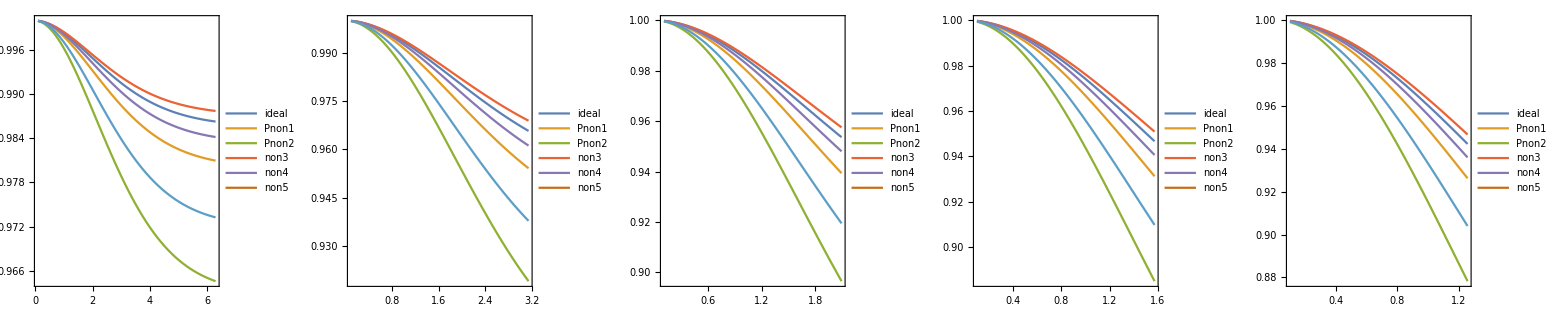

```mathematica
Grid[
{Table[Plot[{𝒫Ωt/.Ω->ΩΩ,𝒫Ωtnonideal/.Ω->ΩΩ,𝒫Ωtnonideal2/.Ω->ΩΩ,𝒫Ωtnonideal3/.Ω->ΩΩ,𝒫Ωtnonideal4/.Ω->ΩΩ,,𝒫Ωtnonideal5/.Ω->ΩΩ},{t,0.1,π/(2*2.5*ΩΩ)},PlotRange->All, PlotLegends->legend[{"ideal","Pnon1","Pnon2","non3","non4","non5"},{0.3,0.4}]],{ΩΩ,{0.1,0.2,0.3,0.4,0.5}}]}

]
```

### 2) Fidelity for t_pulse = t_g = π/(2 Ω_g) = π/(2 r_geΩ)☑

#### a) Simplified analytical expressions and plots

We set t = π/2Ωg=π/(2λΩ), here we define the functions as in the chapter. The expression for the fidelity is given by:

```mathematica
fx = (1+(Ωe/γ)^2+(Ωg/γ)^2)/((1+4(ΔΩm/γ)^2)(1+4(ΔΩp/γ)^2))/.ΔΩm->(Ωg-Ωe)/2/.ΔΩp->(Ωg+Ωe)/2//cf(*ok*)
```

(γ^2 (γ^2+Ωe^2+Ωg^2))/((γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))

```mathematica
fyz = (1/(1+(Ωe/γ)^2)-(ΔΩm/γ)/(1+4(ΔΩm/γ)^2)-(ΔΩp/γ)/(1+4(ΔΩp/γ)^2))/.ΔΩm->(Ωg-Ωe)/2/.ΔΩp->(Ωg+Ωe)/2//cf(*ok*)
```

1/(1+Ωe^2/γ^2)-(γ Ωg (γ^2-Ωe^2+Ωg^2))/((γ^2+(Ωe-Ωg)^2) (γ^2+(Ωe+Ωg)^2))

I denote the fidelity as written in the chapter by ℱch:

```mathematica
ℱch = 1/2+nx/2 fx-(ny nz)/2 fyz//cf
```

1/4 (2+γ (-(2 ny nz γ)/(γ^2+Ωe^2)+(nx γ+ny nz (-Ωe+Ωg))/(γ^2+(Ωe-Ωg)^2)+(nx γ+ny nz (Ωe+Ωg))/(γ^2+(Ωe+Ωg)^2)))

```mathematica
ℱch=ℱch/.Ωe->Ω/.Ωg->λ Ω//cf
```

1/4 (2+γ (-(2 ny nz γ)/(γ^2+Ω^2)+(nx γ+ny nz (-1+λ) Ω)/(γ^2+(-1+λ)^2 Ω^2)+(nx γ+ny nz (1+λ) Ω)/(γ^2+(Ω+λ Ω)^2)))

Contour plot in the perfect alignement condition:

```mathematica
ℱλΩ=ℱch/.idealalignementparamaters
```

1/4 (2+1/(1+(-1+λ)^2 Ω^2)+1/(1+(Ω+λ Ω)^2))

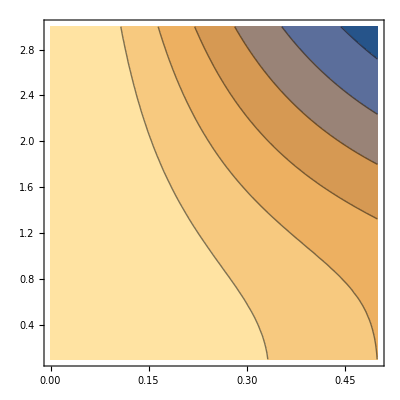

```mathematica
ContourPlot[ℱλΩ,{Ω,0.,0.5},{λ,0.1,3.}]
```

Super ideal situation marked with the dashed line, where λ=1:

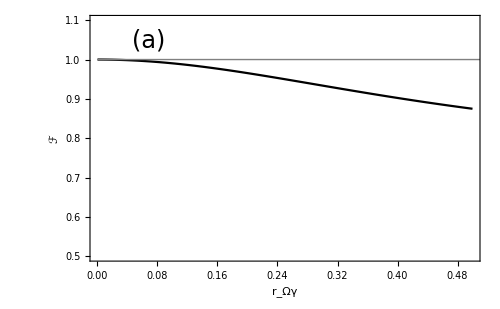

```mathematica
plot1=Plot[ℱλΩ/.λ->1,{Ω,0.,0.5},
PlotRange->{All,{0.5,1.1}},

FrameLabel->{Style["r_Ωγ",FontFamily->"Times",FontSize->fontsize,Black],Style["ℱ",FontFamily->"Times",FontSize->fontsize,Black]},LabelStyle->Directive[FontFamily->"Times",FontSize->fontsize,Black],

PlotStyle->{Black},

Epilog->{
{Text[Style["(a)",FontSize->fontsize,FontFamily->"Times",FontColor->Black],Scaled[{0.15,0.9}]]},(*Horizontal line*){Gray,Line[{{0,1},{1,1}}]}},

ImageSize->500]
Export[overleafNotespath<>"Fidelity-ideal-protocol-conditions.pdf",plot1];
Export[overleafDrafpath<>"Fidelity-ideal-protocol-conditions.pdf",plot1];
(*Save in every overleaf project these images are needed
Do[
Export[PlotsPath<>"Fidelity-ideal-protocol-conditions.pdf",plot],{PlotsPath,pathsList}]*)
```

We observe that the ideal conditions require that r_Ωγ<<1. The fidelity is close to one as long as Ω/γ<0.1. As Ω increases it is deteriorate.

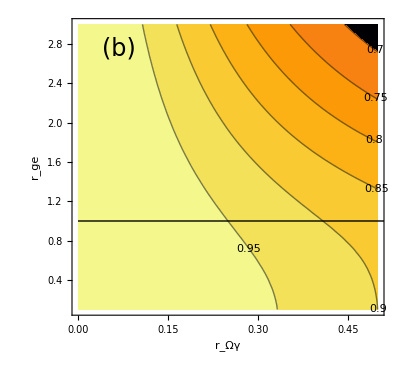

```mathematica
Module[{cf},
cf= MPLColorMap["Inferno"];
plot2=
ContourPlot[ℱλΩ,{Ω,0.,0.5},{λ,0.1,3.},
AspectRatio->7/7.5,
PlotRange->All,

FrameLabel->{Style["r_Ωγ",FontFamily->"Times",FontSize->fontsize,Black],Style["r_ge",FontFamily->"Times",FontSize->fontsize,Black]},
LabelStyle->Directive[FontFamily->"Times",FontSize->fontsize,Black],

ColorFunction->cf,
ContourLabels->All,
ColorFunctionScaling->False,

(*PlotLegends->Placed[BarLegend[{cf,{0,1}},LegendLabel->Style["ℱ",FontFamily->"Times",FontSize->fontsize,Black]],Right],
*)
Epilog->{
{Text[Style["(b)",FontSize->fontsize,FontFamily->"Times",FontColor->Black],Scaled[{0.15,0.9}]]},(*Horizontal line*){Line[{{0,1},{1,1}}]}},

ImageSize->400]
]
Export[overleafNotespath
<>"fig1b.pdf",plot2];
```

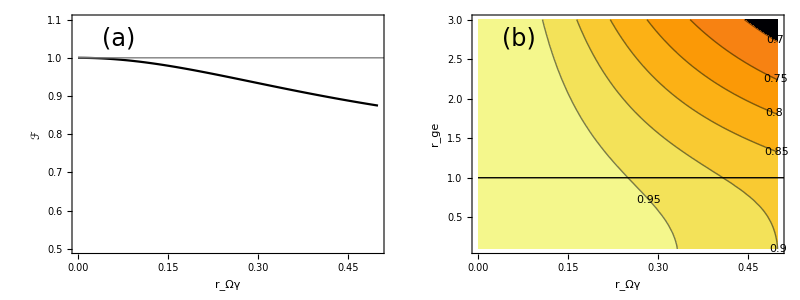

```mathematica
bothIdealscenariotg = Grid[{{plot1,plot2}}]
savePlot["bothIdealscenariotg.pdf",bothIdealscenariotg]
```

### 3) Fidelity for t_pulse = t_optimal

#### a) Finding t_optimal

```mathematica
Fidelity=ℱt /.γ->1//Simplify
```

1/2 (1+(ny nz (-1-2 (1+λ^2) Ω^2+(1+Ω^2) (1+(1+λ^2) Ω^2) Cos[t λ Ω]+λ Ω Sin[t λ Ω]))/((1+Ω^2) (1+(-1+λ)^2 Ω^2) (1+(1+λ)^2 Ω^2))+(nx (-λ Ω (1+(-1+λ^2) Ω^2) Cos[t λ Ω]+(1+(1+λ^2) Ω^2) Sin[t λ Ω]))/(1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))

```mathematica
approxf=Fidelity/.{Ω^2->0,Ω^4->0}(*Get rid of all the higher order terms*)
```

1/2 (1+nx (-λ Ω Cos[t λ Ω]+Sin[t λ Ω])+ny nz (-1+Cos[t λ Ω]+λ Ω Sin[t λ Ω]))

```mathematica
derivativeapproxFidelity = D[approxf,t]
```

1/2 (ny nz (λ^2 Ω^2 Cos[t λ Ω]-λ Ω Sin[t λ Ω])+nx (λ Ω Cos[t λ Ω]+λ^2 Ω^2 Sin[t λ Ω]))

```mathematica
approxderivative = derivativeapproxFidelity/.{Ω^2->0,Ω^4->0}(*Get rid of all the higher order terms*)
```

1/2 (nx λ Ω Cos[t λ Ω]-ny nz λ Ω Sin[t λ Ω])

```mathematica
equation[t_?NumericQ]:=1/2 (nx λ Ω Cos[t λ Ω]-ny nz λ Ω Sin[t λ Ω])
sol=FindRoot[{equation[t]==0,nx>0,ny>0,nz>0,λ>0,Ω>0},{t,0}]
tVal=t/. sol
```

FindRoot::eqlist: In the first argument {equation[t]==0,nx>0,ny>0,nz>0,λ>0,Ω>0} only some of the components are equations.

FindRoot[{equation[t]==0,nx>0,ny>0,nz>0,λ>0,Ω>0},{t,0}]

FindRoot::eqlist: In the first argument {equation[t]==0,nx>0,ny>0,nz>0,λ>0,Ω>0} only some of the components are equations.

ReplaceAll::reps: {FindRoot[{equation[t]==0,nx>0,ny>0,nz>0,λ>0,Ω>0},{t,0}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::eqlist: In the first argument {equation[t]==0,nx>0,ny>0,nz>0,λ>0,Ω>0} only some of the components are equations.

ReplaceAll::reps: {FindRoot[{equation[t]==0,nx>0,ny>0,nz>0,λ>0,Ω>0},{t,0}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

t/.FindRoot[{equation[t]==0,nx>0,ny>0,nz>0,λ>0,Ω>0},{t,0}]

```mathematica
Solve[1/2 (nx λ Ω Cos[t λ Ω]-ny nz λ Ω Sin[t λ Ω])==0&&nx>0&&ny>0&&nz>0,t]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[1/2 (nx λ Ω Cos[t λ Ω]-ny nz λ Ω Sin[t λ Ω])==0&&nx>0&&ny>0&&nz>0,t]

```mathematica
T/.sol/.{nx^2ny^2->0,nx^2nz^2->0,nz^2ny^2->0}
```

{ConditionalExpression[(ArcTan[-(ny nz-nx Ωg)/(√(nx^2+nx^2 Ωg^2)),((nx ny nz)/(√(nx^2 (1+Ωg^2)))-(nx^2 Ωg)/(√(nx^2 (1+Ωg^2)))-(nx ny nz Ωg^2)/(√(nx^2 (1+Ωg^2))))/(-ny nz+nx Ωg)]+2 π C[1])/Ωg,C[1]∈Integers],ConditionalExpression[(ArcTan[(ny nz-nx Ωg)/(√(nx^2+nx^2 Ωg^2)),(-(nx ny nz)/(√(nx^2 (1+Ωg^2)))+(nx^2 Ωg)/(√(nx^2 (1+Ωg^2)))+(nx ny nz Ωg^2)/(√(nx^2 (1+Ωg^2))))/(-ny nz+nx Ωg)]+2 π C[1])/Ωg,C[1]∈Integers]}

```mathematica
trial=ArcTan[-(ny nz-nx Ωg)/(√(nx^2+nx^2 Ωg^2)),((nx ny nz)/(√(nx^2 (1+Ωg^2)))-(nx^2 Ωg)/(√(nx^2 (1+Ωg^2)))-(nx ny nz Ωg^2)/(√(nx^2 (1+Ωg^2))))/(-ny nz+nx Ωg)]/Ωg//FullSimplify
```

ArcTan[(-ny nz+nx Ωg)/(√(nx^2 (1+Ωg^2))),-(nx (nx Ωg+ny nz (-1+Ωg^2)))/((-ny nz+nx Ωg) √(nx^2 (1+Ωg^2)))]/Ωg

```mathematica
Fidelity/.{T->Pi/Ωg-ArcTan[nx/(nx Ωg-ny nz)]/Ωg}
```

(-ny nz (Ωe^4-2 Ωe^2 (-1+Ωg^2)+(1+Ωg^2)^2)+(1+Ωe^2) (nx Ωg (-1+Ωe^2-Ωg^2)+ny nz (1+Ωe^2+Ωg^2)) Cos[Ωg (π/Ωg-ArcTan[nx/(-ny nz+nx Ωg)]/Ωg)]+(1+Ωe^2) (ny nz Ωg (1-Ωe^2+Ωg^2)+nx (1+Ωe^2+Ωg^2)) Sin[Ωg (π/Ωg-ArcTan[nx/(-ny nz+nx Ωg)]/Ωg)])/(2 (1+Ωe^2) (1+Ωe^2-2 Ωe Ωg+Ωg^2) (1+Ωe^2+2 Ωe Ωg+Ωg^2))

#### b) Analytical expression and plots

Components of the fidelity as a function of time is given by:

```mathematica
Ωs={ΔΩm->(Ωg-Ωe)/2,ΔΩp->(Ωg+Ωe)/2};
fxt =  (1+(Ωe/γ)^2+ (Ωg/γ)^2)/((1+4(ΔΩm/γ)^2)(1+4(ΔΩp/γ)^2))Sin[Ωg t]-(1-(Ωe/γ)^2+ (Ωg/γ)^2)/((1+4(ΔΩm/γ)^2)(1+4(ΔΩp/γ)^2))Ωg/γ Cos[Ωg t]/.Ωs/.Ωe->Ω/.Ωg->λ Ω//cf;

fyzt=((Ωg/γ)Sin[Ωg t]-1-2(Ωe/γ)^2-2(Ωg/γ)^2)/((1+(Ωe/γ)^2)(1+4(ΔΩm/γ)^2)(1+4(ΔΩp/γ)^2))+(1+(Ωe/γ)^2+(Ωg/γ)^2)/((1+4(ΔΩm/γ)^2)(1+4(ΔΩp/γ)^2))Cos[Ωg t]/.Ωs/.Ωe->Ω/.Ωg->λ Ω//cf;

ℱt =1/2+(ny nz)/2 fyzt+nx/2 fxt //cf(*I'm changing the - to +*)
```

1/2 (1+(nx γ (-λ Ω (γ^2+(-1+λ^2) Ω^2) Cos[t λ Ω]+γ (γ^2+(1+λ^2) Ω^2) Sin[t λ Ω]))/(γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4)+(ny nz (γ^2 (γ^2+Ω^2) (γ^2+(1+λ^2) Ω^2) Cos[t λ Ω]-γ^4 (γ^2+2 (1+λ^2) Ω^2-γ λ Ω Sin[t λ Ω])))/((γ^2+Ω^2) (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2)))

#### Collecting terms to simplify

```mathematica
expression= fyzt//Expand
```

-γ^6/((γ^2+Ω^2) (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2))-(2 γ^4 Ω^2)/((γ^2+Ω^2) (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2))-(2 γ^4 λ^2 Ω^2)/((γ^2+Ω^2) (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2))+(γ^6 Cos[t λ Ω])/((γ^2+Ω^2) (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2))+(2 γ^4 Ω^2 Cos[t λ Ω])/((γ^2+Ω^2) (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2))+(γ^4 λ^2 Ω^2 Cos[t λ Ω])/((γ^2+Ω^2) (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2))+(γ^2 Ω^4 Cos[t λ Ω])/((γ^2+Ω^2) (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2))+(γ^2 λ^2 Ω^4 Cos[t λ Ω])/((γ^2+Ω^2) (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2))+(γ^5 λ Ω Sin[t λ Ω])/((γ^2+Ω^2) (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2))

```mathematica
constant = -γ^6/((γ^2+Ω^2) (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2))-(2 γ^4 Ω^2)/((γ^2+Ω^2) (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2))-(2 γ^4 λ^2 Ω^2)/((γ^2+Ω^2) (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2))//cf
```

-((γ^4 (γ^2+2 (1+λ^2) Ω^2))/((γ^2+Ω^2) (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2)))

```mathematica
sin=(γ^5 λ Ω Sin[t λ Ω])/((γ^2+Ω^2) (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2))//cf
```

(γ^5 λ Ω Sin[t λ Ω])/((γ^2+Ω^2) (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2))

```mathematica
cos=(γ^6 Cos[t λ Ω])/((γ^2+Ω^2) (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2))+(2 γ^4 Ω^2 Cos[t λ Ω])/((γ^2+Ω^2) (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2))+(γ^4 λ^2 Ω^2 Cos[t λ Ω])/((γ^2+Ω^2) (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2))+(γ^2 Ω^4 Cos[t λ Ω])/((γ^2+Ω^2) (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2))+(γ^2 λ^2 Ω^4 Cos[t λ Ω])/((γ^2+Ω^2) (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2))//cf
```

(γ^2 (γ^2+(1+λ^2) Ω^2) Cos[t λ Ω])/(γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4)

### 4) Consistency check: comparing ℱanalytical with ℱapproximated

```mathematica
Ωs={ΔΩm->(Ωg-Ωe)/2,ΔΩp->(Ωg+Ωe)/2};
fxt =  (1+(Ωe/γ)^2+ (Ωg/γ)^2)/((1+4(ΔΩm/γ)^2)(1+4(ΔΩp/γ)^2))Sin[Ωg t]-(1-(Ωe/γ)^2+ (Ωg/γ)^2)/((1+4(ΔΩm/γ)^2)(1+4(ΔΩp/γ)^2))Ωg/γ Cos[Ωg t]/.Ωs/.Ωe->Ω/.Ωg->λ Ω//cf;

fyzt=((Ωg/γ)Sin[Ωg t]-1-2(Ωe/γ)^2-2(Ωg/γ)^2)/((1+(Ωe/γ)^2)(1+4(ΔΩm/γ)^2)(1+4(ΔΩp/γ)^2))+(1+(Ωe/γ)^2+(Ωg/γ)^2)/((1+4(ΔΩm/γ)^2)(1+4(ΔΩp/γ)^2))Cos[Ωg t]/.Ωs/.Ωe->Ω/.Ωg->λ Ω//cf;

ℱt =1/2+(ny nz)/2 fyzt+nx/2 fxt //cf(*I'm changing the - to +*)
```

1/2 (1+(nx γ (-λ Ω (γ^2+(-1+λ^2) Ω^2) Cos[t λ Ω]+γ (γ^2+(1+λ^2) Ω^2) Sin[t λ Ω]))/(γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4)+(ny nz (γ^2 (γ^2+Ω^2) (γ^2+(1+λ^2) Ω^2) Cos[t λ Ω]-γ^4 (γ^2+2 (1+λ^2) Ω^2-γ λ Ω Sin[t λ Ω])))/((γ^2+Ω^2) (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2)))

```mathematica
coeffs1=Collect[fxt,{Sin[_],Cos[_]},Simplify]/.λ->rge/.γ->1/.Ω->rΩγ
coeffs2=Collect[fyzt,{Sin[_],Cos[_]},Simplify]/.λ->rge/.γ->1/.Ω->rΩγ
```

-(rge rΩγ (1+(-1+rge^2) rΩγ^2) Cos[rge rΩγ t])/(1+2 (1+rge^2) rΩγ^2+(-1+rge^2)^2 rΩγ^4)+((1+(1+rge^2) rΩγ^2) Sin[rge rΩγ t])/(1+2 (1+rge^2) rΩγ^2+(-1+rge^2)^2 rΩγ^4)

-(1+2 (1+rge^2) rΩγ^2)/((1+rΩγ^2) (1+(-1+rge)^2 rΩγ^2) (1+(1+rge)^2 rΩγ^2))+((1+(1+rge^2) rΩγ^2) Cos[rge rΩγ t])/((1+(-1+rge)^2 rΩγ^2) (1+(1+rge)^2 rΩγ^2))+(rge rΩγ Sin[rge rΩγ t])/((1+rΩγ^2) (1+(-1+rge)^2 rΩγ^2) (1+(1+rge)^2 rΩγ^2))

```mathematica
k00=-(1+2 (1+rge^2) rΩγ^2)/((1+rΩγ^2) (1+(-1+rge)^2 rΩγ^2) (1+(1+rge)^2 rΩγ^2));
k11 =(rge rΩγ)/((1+rΩγ^2) (1+(-1+rge)^2 rΩγ^2) (1+(1+rge)^2 rΩγ^2))
k22 =(1+(1+rge^2) rΩγ^2)/((1+(-1+rge)^2 rΩγ^2) (1+(1+rge)^2 rΩγ^2));
k33 =(1+(1+rge^2) rΩγ^2)/(1+2 (1+rge^2) rΩγ^2+(-1+rge^2)^2 rΩγ^4)
k44 =-(rge rΩγ (1+(-1+rge^2) rΩγ^2))/(1+2 (1+rge^2) rΩγ^2+(-1+rge^2)^2 rΩγ^4);
```

(rge rΩγ)/((1+rΩγ^2) (1+(-1+rge)^2 rΩγ^2) (1+(1+rge)^2 rΩγ^2))

(1+(1+rge^2) rΩγ^2)/(1+2 (1+rge^2) rΩγ^2+(-1+rge^2)^2 rΩγ^4)

```mathematica
fxx = k44 Cos[rge Ω t] + k33 Sin[rge Ω t];
fyz = k00 + k22 Cos[rge Ω t] + k11 Sin[rge Ω t];
```

```mathematica
ℱapk = 1/2+nx/2 fxx+(ny nz)/2 fyz
```

1/2+1/2 ny nz (-(1+2 (1+rge^2) rΩγ^2)/((1+rΩγ^2) (1+(-1+rge)^2 rΩγ^2) (1+(1+rge)^2 rΩγ^2))+((1+(1+rge^2) rΩγ^2) Cos[rge t Ω])/((1+(-1+rge)^2 rΩγ^2) (1+(1+rge)^2 rΩγ^2))+(rge rΩγ Sin[rge t Ω])/((1+rΩγ^2) (1+(-1+rge)^2 rΩγ^2) (1+(1+rge)^2 rΩγ^2)))+1/2 nx (-(rge rΩγ (1+(-1+rge^2) rΩγ^2) Cos[rge t Ω])/(1+2 (1+rge^2) rΩγ^2+(-1+rge^2)^2 rΩγ^4)+((1+(1+rge^2) rΩγ^2) Sin[rge t Ω])/(1+2 (1+rge^2) rΩγ^2+(-1+rge^2)^2 rΩγ^4))

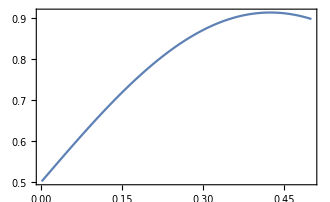

```mathematica
Plot[ℱanalytical/.parIdeal,{Ω,0.001,0.5}]
```

```mathematica
toptimal =2 π/Ωg+ArcTan[(-nx^2 Ωg+ny^2 nz^2 Ωg+nx ny nz (1+2 Ωe^2+Ωg^2))/((nx Ωg-ny nz (1+Ωe^2+Ωg^2))^2)]/Ωg(*π/Ωg-1/Ωg ArcTan[nx/(nx Ωg - ny nz)]*)/.Ωe->Ω/.Ωg->λ Ω
```

(2 π)/(λ Ω)+ArcTan[(-nx^2 λ Ω+ny^2 nz^2 λ Ω+nx ny nz (1+2 Ω^2+λ^2 Ω^2))/((nx λ Ω-ny nz (1+Ω^2+λ^2 Ω^2))^2)]/(λ Ω)

The fidelity as a function of time is given by:

```mathematica
parIdeal ={λ->1,t->4,nx->1,ny->0,nz->0, γ->1};
parNonIdeal1 ={λ->1,t->4,nx->1/√3,ny->1/√3,nz->1/√3, γ->1};
parNonIdeal2 ={λ->1,t->4,nx->0,ny->1/√2,nz->1/√2, γ->1};
```

```mathematica
ℱt/.parIdeal
```

1/2 (1+(-Ω Cos[4 Ω]+(1+2 Ω^2) Sin[4 Ω])/(1+4 Ω^2))

```mathematica
ℱanalytical/.parIdeal
```

1/2 (1+(ⅈ (-ⅇ^(8+4 ⅈ Ω) (1-ⅈ Ω) (1+ⅈ Ω)^2 (1-2 ⅈ Ω)+ⅇ^(4 (2-ⅈ Ω)) (1-ⅈ Ω)^2 (1+ⅈ Ω) (1+2 ⅈ Ω)+ⅇ^(4 (1+ⅈ Ω)) (-ⅈ-Ω) (1+ⅈ Ω) (1+2 ⅈ Ω) Ω+ⅇ^(4 (1-ⅈ Ω)) (1-ⅈ Ω) (1-2 ⅈ Ω) Ω (-ⅈ+Ω)))/(4 ⅇ^8 (1+Ω^2) (1+4 Ω^2) (1/8 (4-4/ⅇ^4+(2 ⅇ^(-4 ⅈ Ω) (1-ⅈ Ω))/(1-2 ⅈ Ω)+(2 ⅈ ⅇ^(4 ⅈ Ω) (-ⅈ+Ω))/(1+2 ⅈ Ω)-(2 ⅇ^(-4 (1-ⅈ Ω)) (1-2 ⅈ Ω-Ω^2))/((1-ⅈ Ω) (1-2 ⅈ Ω))-(2 ⅇ^(-4 (1+ⅈ Ω)) (1+2 ⅈ Ω-Ω^2))/((1+ⅈ Ω) (1+2 ⅈ Ω)))+1/4 (2-2/ⅇ^4-(ⅇ^(-4 ⅈ Ω) (1-ⅈ Ω))/(1-2 ⅈ Ω)-(ⅈ ⅇ^(4 ⅈ Ω) (-ⅈ+Ω))/(1+2 ⅈ Ω)+(ⅇ^(-4 (1-ⅈ Ω)) (1-2 ⅈ Ω-Ω^2))/((1-ⅈ Ω) (1-2 ⅈ Ω))+(ⅇ^(-4 (1+ⅈ Ω)) (1+2 ⅈ Ω-Ω^2))/((1+ⅈ Ω) (1+2 ⅈ Ω)))))-(ⅈ (ⅇ^(4 (2+ⅈ Ω)) (1-ⅈ Ω) (1+ⅈ Ω)^2 (1-2 ⅈ Ω)-ⅇ^(8-4 ⅈ Ω) (1-ⅈ Ω)^2 (1+ⅈ Ω) (1+2 ⅈ Ω)+ⅇ^(4 (1-ⅈ Ω)) (ⅈ-Ω) (1-ⅈ Ω) (1-2 ⅈ Ω) Ω+ⅇ^(4 (1+ⅈ Ω)) (1+ⅈ Ω) (1+2 ⅈ Ω) Ω (ⅈ+Ω)))/(4 ⅇ^8 (1+Ω^2) (1+4 Ω^2) (1/8 (4-4/ⅇ^4+(2 ⅇ^(-4 ⅈ Ω) (1-ⅈ Ω))/(1-2 ⅈ Ω)+(2 ⅈ ⅇ^(4 ⅈ Ω) (-ⅈ+Ω))/(1+2 ⅈ Ω)-(2 ⅇ^(-4 (1-ⅈ Ω)) (1-2 ⅈ Ω-Ω^2))/((1-ⅈ Ω) (1-2 ⅈ Ω))-(2 ⅇ^(-4 (1+ⅈ Ω)) (1+2 ⅈ Ω-Ω^2))/((1+ⅈ Ω) (1+2 ⅈ Ω)))+1/4 (2-2/ⅇ^4-(ⅇ^(-4 ⅈ Ω) (1-ⅈ Ω))/(1-2 ⅈ Ω)-(ⅈ ⅇ^(4 ⅈ Ω) (-ⅈ+Ω))/(1+2 ⅈ Ω)+(ⅇ^(-4 (1-ⅈ Ω)) (1-2 ⅈ Ω-Ω^2))/((1-ⅈ Ω) (1-2 ⅈ Ω))+(ⅇ^(-4 (1+ⅈ Ω)) (1+2 ⅈ Ω-Ω^2))/((1+ⅈ Ω) (1+2 ⅈ Ω))))))

```mathematica
ℱapk/.rge->1/.rΩγ->Ω/.parIdeal
```

1/2+1/2 (-(Ω Cos[4 Ω])/(1+4 Ω^2)+((1+2 Ω^2) Sin[4 Ω])/(1+4 Ω^2))

```mathematica
parIdeal
```

{λ→1,t→4,nx→1,ny→0,nz→0,γ→1}

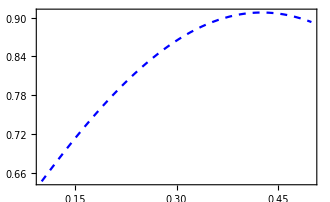

```mathematica
Plot[{ℱt/.rge->1/.rΩγ->Ω/.parIdeal},{Ω,0.1,0.5},
PlotStyle->{Red,{Black,Dashed},Blue},PlotRange->All]
```

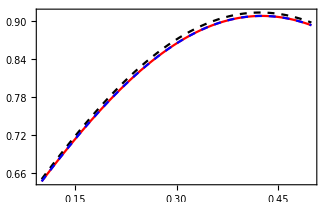

```mathematica
Plot[{ℱt/.parIdeal,ℱanalytical/.parIdeal,ℱapk/.rge->1/.rΩγ->Ω/.parIdeal},{Ω,0.1,0.5},
PlotStyle->{Red,{Black,Dashed},{Blue,Dashed}},PlotRange->All]
```

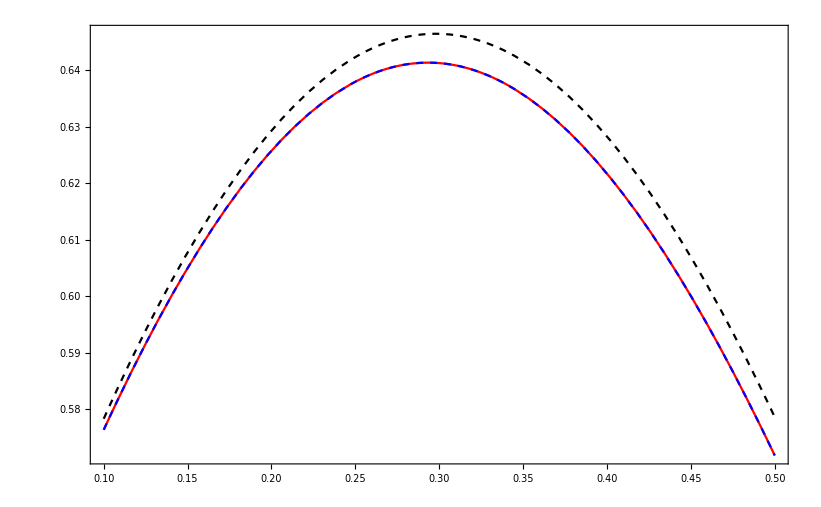

```mathematica
Plot[{ℱt/.parNonIdeal1,ℱanalytical/.parNonIdeal1,ℱapk/.rge->1/.rΩγ->Ω/.parNonIdeal1},{Ω,0.1,0.5},
PlotStyle->{Red,{Black,Dashed},{Blue,Dashed}}]
```

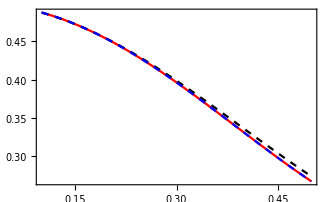

```mathematica
Plot[{ℱt/.parNonIdeal2,ℱanalytical/.parNonIdeal2,ℱapk/.rge->1/.rΩγ->Ω/.parNonIdeal2},{Ω,0.1,0.5},
PlotStyle->{Red,{Black,Dashed},{Blue,Dashed}}]
```

### 5) Deriving optimal time

We begin with the approximated expression of the fidelity:

```mathematica
ℱapprox = 1/2+nx/2(k1 Cos[reg Ω t]-k2 Sin[reg Ω t])+(ny nz)/2(k3+k4 Cos[reg Ω t]+k5 Sin[reg Ω t] )
```

1/2+1/2 nx (k1 Cos[reg t Ω]-k2 Sin[reg t Ω])+1/2 ny nz (k3+k4 Cos[reg t Ω]+k5 Sin[reg t Ω])

Deriving with respect to time we obtain:

```mathematica
derivativeℱapprox=(D[ℱapprox, t])//FullSimplify
```

-1/2 reg Ω ((k2 nx-k5 ny nz) Cos[reg t Ω]+(k1 nx+k4 ny nz) Sin[reg t Ω])

```mathematica
secondDerivative=D[derivativeℱapprox, t]//cf
```

-1/2 reg^2 Ω^2 ((k1 nx+k4 ny nz) Cos[reg t Ω]+(-k2 nx+k5 ny nz) Sin[reg t Ω])

The coefficients are:

```mathematica
k11 =-(rge rΩγ [1+(rge^2-1)rΩγ^2])/(2(1+rge^2)rΩγ^2+(rge^2-1)rΩγ^2);
k22 = (1+(1+rge^2)rΩγ^2)/(1+2(1+rge^2)rΩγ^2+(rge^2-1)rΩγ^2);
k33 = -(1+2(rge^2+1)rΩγ^2)/((1+rΩγ)(1+(rge^2-1)rΩγ^2)(rge^2+1)rΩγ^2);
k44 = (rge rΩγ)/((1+rΩγ^2)(1+(rge-1)^2 rΩγ^2)(1+(rge+1)^2 rΩγ^2));
k55 = (1+(1+rge^2)rΩγ^2)/(1+2(rge^2+1)rΩγ^2+(rge^2-1)rΩγ^2);
```

```mathematica
kcoefficients={k1->k11,k2->k22,k3->k33,k4->k44,k5->k55};
```

```mathematica
argArcTg=(k5 ny nz - k2 nx)/(k1 nx+k4 ny nz)/.kcoefficients//cf
toptimal =(2π)/(rge Ω)+ 1/(rge Ω)ArcTan[argArcTg]/.kcoefficients
```

((nx-ny nz) (1+3 rge^2) rΩγ^2 (1+rΩγ^2) (1+3 (1+rge^2) rΩγ^2+(3+2 rge^2+3 rge^4) rΩγ^4+(-1+rge^2)^2 (1+rge^2) rΩγ^6))/(rge (1+(1+3 rge^2) rΩγ^2) (-ny nz (1+3 rge^2) rΩγ^3+nx (1+rΩγ^2) (1+2 (1+rge^2) rΩγ^2+(-1+rge^2)^2 rΩγ^4) rΩγ[1+(-1+rge^2) rΩγ^2]))

(2 π)/(rge Ω)+ArcTan[((nx-ny nz) (1+3 rge^2) rΩγ^2 (1+rΩγ^2) (1+3 (1+rge^2) rΩγ^2+(3+2 rge^2+3 rge^4) rΩγ^4+(-1+rge^2)^2 (1+rge^2) rΩγ^6))/(rge (1+(1+3 rge^2) rΩγ^2) (-ny nz (1+3 rge^2) rΩγ^3+nx (1+rΩγ^2) (1+2 (1+rge^2) rΩγ^2+(-1+rge^2)^2 rΩγ^4) rΩγ[1+(-1+rge^2) rΩγ^2]))]/(rge Ω)

The ideal alignment is given by

```mathematica
idealalignementparamaters={γ->1,nx->1,ny->0,nz->0}
```

{γ→1,nx→1,ny→0,nz→0}

Does the optimal time reduces to the 2π/Ωg if we are in the ideal protocol limits? rΩγ->0 ideally aligned.

```mathematica
test=toptimal/.idealalignementparamaters/.rΩγ->Ω//cf
```

(2 π+ArcCot[(rge (1+(1+3 rge^2) Ω^2) Ω[1+(-1+rge^2) Ω^2])/((1+3 rge^2) Ω^2 (1+(1+rge^2) Ω^2))])/(rge Ω)

```mathematica
test//cf
```

(2 π+ArcCot[(rge (1+(1+3 rge^2) Ω^2) Ω[1+(-1+rge^2) Ω^2])/((1+3 rge^2) Ω^2 (1+(1+rge^2) Ω^2))])/(rge Ω)

Yes!

```mathematica
toptimal/.rΩγ->0
```

(2 π)/(rge Ω)

### Derivating optimal time for average fidelity

```mathematica
fx = k1 Cos[rge*Ω*t]-k2 Sin[rge*Ω*t]
```

k1 Cos[rge t Ω]-k2 Sin[rge t Ω]

```mathematica
D[fx, t]//cf
```

-rge Ω (k2 Cos[rge t Ω]+k1 Sin[rge t Ω])

```mathematica
∂_t %//cf
```

rge^2 Ω^2 (-k1 Cos[rge t Ω]+k2 Sin[rge t Ω])

The coefficients are:

```mathematica
(*k11 =-(rge rΩγ (1+(rge^2-1)rΩγ^2))/(2(1+rge^2)rΩγ^2+(rge^2-1)rΩγ^2);
k22 = (1+(1+rge^2)rΩγ^2)/(1+2(1+rge^2)rΩγ^2+(rge^2-1)rΩγ^2);
k33 = -(1+2(rge^2+1)rΩγ^2)/((1+rΩγ)(1+(rge^2-1)rΩγ^2)(rge^2+1)rΩγ^2);
k44 = (rge rΩγ)/((1+rΩγ^2)(1+(rge-1)^2 rΩγ^2)(1+(rge+1)^2 rΩγ^2));
k55 = (1+(1+rge^2)rΩγ^2)/(1+2(rge^2+1)rΩγ^2+(rge^2-1)rΩγ^2);*)
```

```mathematica
k00=-(1+2 (1+rge^2) rΩγ^2)/((1+rΩγ^2) (1+(-1+rge)^2 rΩγ^2) (1+(1+rge)^2 rΩγ^2));
k11 =(rge rΩγ)/((1+rΩγ^2) (1+(-1+rge)^2 rΩγ^2) (1+(1+rge)^2 rΩγ^2))
k22 =(1+(1+rge^2) rΩγ^2)/((1+(-1+rge)^2 rΩγ^2) (1+(1+rge)^2 rΩγ^2));
k33 =(1+(1+rge^2) rΩγ^2)/(1+2 (1+rge^2) rΩγ^2+(-1+rge^2)^2 rΩγ^4)
k44 =-(rge rΩγ (1+(-1+rge^2) rΩγ^2))/(1+2 (1+rge^2) rΩγ^2+(-1+rge^2)^2 rΩγ^4);
```

(rge rΩγ)/((1+rΩγ^2) (1+(-1+rge)^2 rΩγ^2) (1+(1+rge)^2 rΩγ^2))

(1+(1+rge^2) rΩγ^2)/(1+2 (1+rge^2) rΩγ^2+(-1+rge^2)^2 rΩγ^4)

```mathematica
tstar=1/(rge Ω)ArcTan[k33/k44]+(m π)/(rge Ω)//cf
```

(m π-ArcTan[(1+(1+rge^2) rΩγ^2)/(rge rΩγ+rge (-1+rge^2) rΩγ^3)])/(rge Ω)

```mathematica
lowerboundtstar = 1/(rge Ω)ArcTan[-k44/k33]+(n π)/(rge Ω)//cf
```

(n π+ArcTan[(rge rΩγ (1+(-1+rge^2) rΩγ^2))/(1+(1+rge^2) rΩγ^2)])/(rge Ω)

```mathematica
upperboundtstar = π/(2rge Ω)+(n π)/(rge Ω)
```

π/(2 rge Ω)+(n π)/(rge Ω)

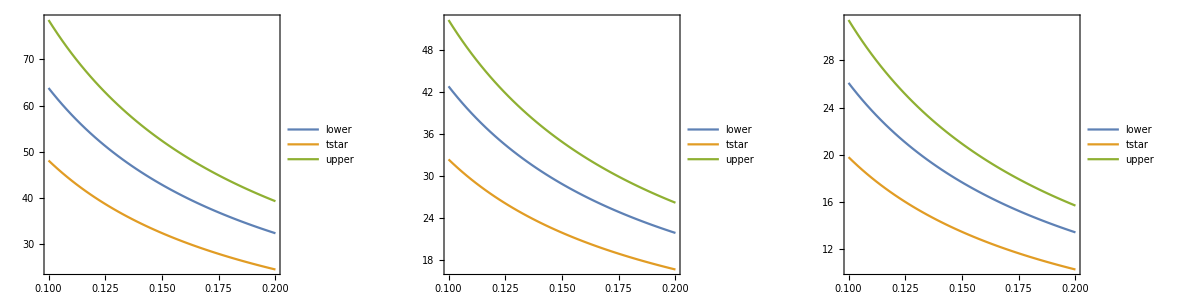

```mathematica
Grid[{Table[Plot[{lowerboundtstar/.rge->rrge/.Ω->rΩγ/.n->2,tstar/.rge->rrge/.Ω->rΩγ/.m->2,upperboundtstar/.rge->rrge/.Ω->rΩγ/.n->2},{rΩγ,0.1,0.2},PlotRange->{All,All(*{-10,30}*)},PlotLegends->legend[{"lower","tstar","upper"},{0.7,0.7}]],
{rrge,{1,1.5,2.5}}]}]
```

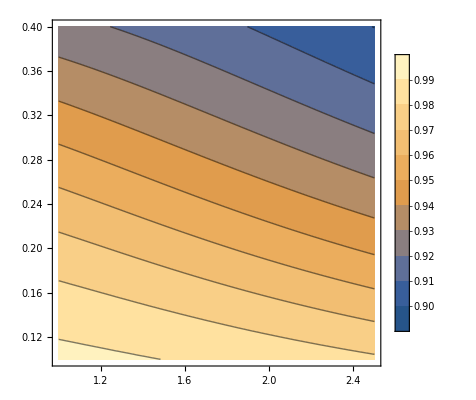
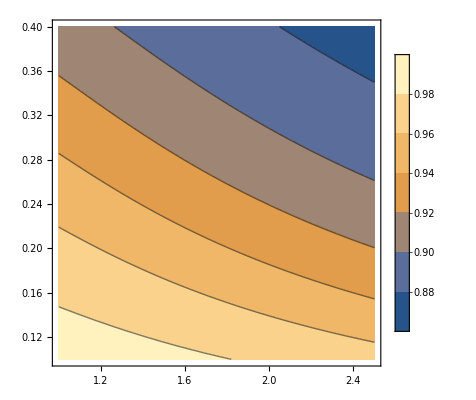
-Graphics- | -Graphics-

```mathematica
Grid[{{ContourPlot[Chop@ℱanalytical/.nx->1/.ny->0/.nz->0/.γ->1/.Ω->rΩγ/.λ->rge/.t->tstar/.m->1/.Ω->rΩγ,{rge,1,2.5},{rΩγ,0.1,0.4},PlotLegends->Automatic],ContourPlot[Chop@ℱanalytical/.nx->1/.ny->0/.nz->0/.γ->1/.Ω->rΩγ/.λ->rge/.t->π/(2 rge Ω)/.Ω->rΩγ,{rge,1,2.5},{rΩγ,0.1,0.4},PlotLegends->Automatic]}}]
```

### 6) Plotting

```mathematica
ℱanalytical
```

(ⅇ^(-t (γ+ⅈ λ Ω)) (ⅇ^(2 t (γ+ⅈ λ Ω)) (-ⅈ nx+ny nz) γ (γ-ⅈ Ω) (γ+ⅈ Ω) (γ-ⅈ (-1+λ) Ω) (γ+ⅈ λ Ω) (γ-ⅈ (1+λ) Ω)+ⅇ^(2 t γ) (nx-ⅈ ny nz) γ (γ-ⅈ Ω) (γ+ⅈ Ω) (γ+ⅈ (-1+λ) Ω) (ⅈ γ+λ Ω) (γ+ⅈ (1+λ) Ω)-2 ⅇ^(2 t γ+ⅈ t λ Ω) ((-1+ny nz) γ^2-Ω^2) (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2)-2 ⅇ^(t (γ+ⅈ λ Ω)) (γ^2+Ω^2) (γ^2+(-1+λ)^2 Ω^2) (γ^2+(1+λ)^2 Ω^2)+ⅇ^(t (γ+ⅈ (-1+λ) Ω)) γ λ (γ-ⅈ Ω) Ω (nx (γ+ⅈ Ω)+ny nz λ Ω) (γ^2-2 ⅈ γ Ω+(-1+λ^2) Ω^2)+ⅇ^(t (γ+ⅈ (1+λ) Ω)) γ λ (γ+ⅈ Ω) Ω (nx (γ-ⅈ Ω)+ny nz λ Ω) (γ^2+2 ⅈ γ Ω+(-1+λ^2) Ω^2)))/(4 (-1+ⅇ^(t γ)) (γ^2+Ω^2) (γ^4+2 γ^2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))

```mathematica
ℱtoptimal=ℱt/.t->toptimal;
```

1/2 (1+(1+Ω^2 (1+λ^2 (2+(-1+λ^2) Ω^2)))/(√(1+λ^2 Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4)))

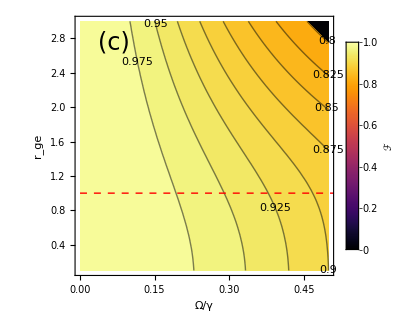

```mathematica
Module[{cf},

cf= MPLColorMap["Inferno"];

plot3=
ContourPlot[ℱλΩ2,{Ω,0.,0.5},{λ,0.1,3.},
PlotRange->All,
AspectRatio->7/7.5,
FrameLabel->{Style["Ω/γ",FontFamily->"Times",FontSize->fontsize,Black],Style["r_ge",FontFamily->"Times",FontSize->fontsize,Black]},LabelStyle->Directive[FontFamily->"Times",FontSize->fontsize,Black],ColorFunction->cf,ContourLabels->All,ColorFunctionScaling->False,PlotLegends->Placed[BarLegend[{cf,{0,1}},LegendLabel->Style["ℱ",FontFamily->"Times",FontSize->fontsize,Black]],Right],Epilog->{
{Text[Style["(c)",FontSize->fontsize,FontFamily->"Times",FontColor->Black],Scaled[{0.15,0.9}]]},

(*Horizontal line*){Red,Dashed,Line[{{0,1},{1,1}}]}},
ImageSize->350]
]
```

```mathematica
λλlist= {1.0,1.5,2.5};
Module[{nhat,parOptimal,xhat},
nhat = Normalize@{1,nn,nn};
xhat = {1,0,0};
parOptimal={γ->1,t-> toptimal,λ->λλ,nx->N[nhat[[1]]],ny->N[nhat[[2]]],nz->N[nhat[[3]]],Ω->ΩΩ};
Do[

fidelitytOptimalcontplot[λλ]=Flatten[Table[{nhat.xhat,N@ΩΩ,Chop@N[ℱtoptimal/.parOptimal]},{ΩΩ,10^-2,0.5,10^-3},{nn,0,0.8,10^-2}],1]

,{λλ,λλlist}]
]
```

```mathematica
λλlist= {1.0,1.5,2.5};
Module[{nhat,partg, xhat},
nhat = Normalize@{1,nn,nn};
xhat = {1,0,0};
partg ={γ->1,t-> π/(2 λ Ω),λ->λλ,nx->N[nhat[[1]]],ny->N[nhat[[2]]],nz->N[nhat[[3]]],Ω->ΩΩ};
Do[

fidelitytgcontplot[λλ]=Flatten[Table[{nhat.xhat,N@ΩΩ,Chop@N[ℱch/.partg]},{ΩΩ,10^-2,0.5,10^-3},{nn,0,0.8,10^-2}],1]

,{λλ,λλlist}]
]
```

```mathematica
Module[{cf,plotSize,frameLabelStyle},

cf=MPLColorMap["Inferno"];
plotSize=500;
frameLabelStyle={FontSize->fontsize,FontColor->Black,FontFamily->"Times"};
contourplotsInnerProdTg=Grid[{Table[
ListContourPlot[fidelitytgcontplot[λλlist[[j]]],
PlotRange->All,FrameLabel->{Style["⟨(n̂)_g,x̂⟩",FontFamily->"Times",FontSize->fontsize,Black],Style["Ω/γ",FontFamily->"Times",FontSize->fontsize,Black]},LabelStyle->Directive[FontFamily->"Times",FontSize->fontsize,Black],ColorFunction->cf,ContourLabels->All,ColorFunctionScaling->False,
ImageSize->plotSize,
Epilog->{Text[Style[alphabetlabel[[j]],FontSize->fontsize,FontFamily->"Times",FontColor->Black],Scaled[{0.85,0.9}]]},
PlotLegends->Automatic,PlotLabel->Style["r="<>ToString[λλlist[[j]]],FontSize->fontsize,FontFamily->"Times",FontColor->Black]
]
,{j,1,Length@λλlist}]}]
]
savePlot["Fidelity-ContPlot-InnerProdTg.jpg",contourplotsInnerProdTg]
```

-Graphics- | -Graphics- | -Graphics-

```mathematica
Module[{cf,plotSize,frameLabelStyle},

cf=MPLColorMap["Inferno"];
plotSize=500;
frameLabelStyle={FontSize->fontsize,FontColor->Black,FontFamily->"Times"};
contourplotsInnerProdTOptimal=Grid[{Table[
ListContourPlot[fidelitytOptimalcontplot[λλlist[[j]]],
PlotRange->All,FrameLabel->{Style["⟨(n̂)_g,x̂⟩",FontFamily->"Times",FontSize->fontsize,Black],Style["Ω/γ",FontFamily->"Times",FontSize->fontsize,Black]},LabelStyle->Directive[FontFamily->"Times",FontSize->fontsize,Black],ColorFunction->cf,ContourLabels->All,ColorFunctionScaling->False,
ImageSize->plotSize,
Epilog->{Text[Style[alphabetlabel[[j+3]],FontSize->fontsize,FontFamily->"Times",FontColor->Black],Scaled[{0.85,0.9}]]},
PlotLegends->Automatic,PlotLabel->Style["r="<>ToString[λλlist[[j]]],FontSize->fontsize,FontFamily->"Times",FontColor->Black]
]
,{j,1,Length@λλlist}]}]
]
savePlot["Fidelity-ContPlot-InnerProdTOptimal.jpg",contourplotsInnerProdTOptimal]
```

-Graphics- | -Graphics- | -Graphics-

### 7) Fidelity for t_pulse = t_optimal: numerical

The questions we answer here are:	
	1) Is there an optimal time that maximizes the fidelity? If so,
	2) what is the ration between it and the t_g? n_toptimal = t_optimal /  t_g
This does not provide an analytical expression for t_optimal but informs us “how many t_g’s” we should actually wait to have the maximum fidelity, which is already a valuable information. This is important information, the experimentalists do not have access to the direction of the parasitic magnetic fields, but they do can infer t_g.

```mathematica
idealalignementparamaters
```

{γ→1,nx→1,ny→0,nz→0}

((nx-ny nz) (1+3 rge^2) rΩγ^2 (1+rΩγ^2) (1+3 (1+rge^2) rΩγ^2+(3+2 rge^2+3 rge^4) rΩγ^4+(-1+rge^2)^2 (1+rge^2) rΩγ^6))/(rge (1+(1+3 rge^2) rΩγ^2) (-ny nz (1+3 rge^2) rΩγ^3+nx (1+rΩγ^2) (1+2 (1+rge^2) rΩγ^2+(-1+rge^2)^2 rΩγ^4) rΩγ[1+(-1+rge^2) rΩγ^2]))

(2 π)/(rge Ω)+ArcTan[((nx-ny nz) (1+3 rge^2) rΩγ^2 (1+rΩγ^2) (1+3 (1+rge^2) rΩγ^2+(3+2 rge^2+3 rge^4) rΩγ^4+(-1+rge^2)^2 (1+rge^2) rΩγ^6))/(rge (1+(1+3 rge^2) rΩγ^2) (-ny nz (1+3 rge^2) rΩγ^3+nx (1+rΩγ^2) (1+2 (1+rge^2) rΩγ^2+(-1+rge^2)^2 rΩγ^4) rΩγ[1+(-1+rge^2) rΩγ^2]))]/(rge Ω)

```mathematica
toptimalapprox=(2 π)/(rge Ω)+ArcTan[((nx-ny nz) (1+3 rge^2) rΩγ^2 (1+rΩγ^2) (1+3 (1+rge^2) rΩγ^2))/(rge (1+(1+3 rge^2) rΩγ^2) (nx (1+rΩγ^2) (1+2 (1+rge^2) rΩγ^2) rΩγ))]/(rge Ω)//cf
```

(2 π+ArcTan[((nx-ny nz) (1+3 rge^2) rΩγ (1+3 (1+rge^2) rΩγ^2))/(nx rge (1+2 (1+rge^2) rΩγ^2) (1+(1+3 rge^2) rΩγ^2))])/(rge Ω)

```mathematica
ℱanalytical/.λ->rge/.γ->1/.t->toptimal/.rΩγ->Ω/.idealalignementparamaters
```

(ⅇ^(-((1+ⅈ Ω) ((2 π)/Ω+ArcTan[(4 Ω^2 (1+6 Ω^2+8 Ω^4))/((1+4 Ω^2)^2 Ω[1])]/Ω))) (-ⅈ ⅇ^(2 (1+ⅈ Ω) ((2 π)/Ω+ArcTan[(4 Ω^2 (1+6 Ω^2+8 Ω^4))/((1+4 Ω^2)^2 Ω[1])]/Ω)) (1-ⅈ Ω) (1+ⅈ Ω)^2 (1-2 ⅈ Ω)+ⅇ^((2 π)/Ω+ArcTan[(4 Ω^2 (1+6 Ω^2+8 Ω^4))/((1+4 Ω^2)^2 Ω[1])]/Ω) (1-ⅈ Ω) (1+ⅈ Ω) (1-2 ⅈ Ω) Ω+ⅇ^((1+2 ⅈ Ω) ((2 π)/Ω+ArcTan[(4 Ω^2 (1+6 Ω^2+8 Ω^4))/((1+4 Ω^2)^2 Ω[1])]/Ω)) (1-ⅈ Ω) (1+ⅈ Ω) (1+2 ⅈ Ω) Ω+ⅇ^(2 ((2 π)/Ω+ArcTan[(4 Ω^2 (1+6 Ω^2+8 Ω^4))/((1+4 Ω^2)^2 Ω[1])]/Ω)) (1-ⅈ Ω) (1+ⅈ Ω) (1+2 ⅈ Ω) (ⅈ+Ω)-2 ⅇ^(2 ((2 π)/Ω+ArcTan[(4 Ω^2 (1+6 Ω^2+8 Ω^4))/((1+4 Ω^2)^2 Ω[1])]/Ω)+ⅈ Ω ((2 π)/Ω+ArcTan[(4 Ω^2 (1+6 Ω^2+8 Ω^4))/((1+4 Ω^2)^2 Ω[1])]/Ω)) (-1-Ω^2) (1+4 Ω^2)-2 ⅇ^((1+ⅈ Ω) ((2 π)/Ω+ArcTan[(4 Ω^2 (1+6 Ω^2+8 Ω^4))/((1+4 Ω^2)^2 Ω[1])]/Ω)) (1+Ω^2) (1+4 Ω^2)))/(4 (-1+ⅇ^((2 π)/Ω+ArcTan[(4 Ω^2 (1+6 Ω^2+8 Ω^4))/((1+4 Ω^2)^2 Ω[1])]/Ω)) (1+Ω^2) (1+4 Ω^2))

```mathematica
Plot[Chop@N[ℱanalytical/.λ->rge/.γ->1/.t->toptimal/.rΩγ->Ω/.idealalignementparamaters],{Ω,0,0.4}]
```

-Graphics-

```mathematica
toptimalapprox/.idealalignementparamaters//cf
```

(2 π+ArcTan[(4 (rΩγ+6 rΩγ^3))/((1+4 rΩγ^2)^2)])/Ω

```mathematica
(2 π)/(λ Ω)+ArcTan[(-nx^2 λ Ω+ny^2 nz^2 λ Ω+nx ny nz (1+λ^2 Ω^2+Ω^2 (2+4 λ^2 Ω^2)))/((nx λ Ω (-1+Ω^2)+ny nz (1+Ω^2+λ^2 Ω^2))^2)]/(λ Ω)//cf
```

(2 π+ArcTan[(-nx^2 λ Ω+ny^2 nz^2 λ Ω+nx ny nz (1+(2+λ^2) Ω^2+4 λ^2 Ω^4))/((nx λ Ω (-1+Ω^2)+ny nz (1+(1+λ^2) Ω^2))^2)])/(λ Ω)

```mathematica
toptimal2=Series[toptimal,{rΩγ,0,3}]//cf
```

π/Ω+((1/rge+3 rge) rΩγ^2)/(Ω rΩγ[1])+O[rΩγ]^4

### 8) New plots with the analytical expression

```mathematica
ntest = Normalize@{1,0.5,0.5}
```

{0.816497,0.408248,0.408248}

```mathematica
idealprotocolparamaters = {γ->1,nx->1,ny->0,nz->0,λ->1,rge->1};
idealalignementparamaters = {γ->1,nx->1,ny->0,nz->0,rge->1};
nonidealprotocolparamaters = {γ->1,nx->ntest⟦1⟧,ny->ntest⟦2⟧,nz->ntest⟦3⟧,λ->2.5,rge->1};(*λ can change*)
```

```mathematica
Ω[1]
```

Ω[1]

```mathematica
ℱanalytical/.t->ArcTan[((1+(1+rge^2) rΩγ^2) ((-1+rge^2) rΩγ^2+2 (1+rge^2) rΩγ^2))/(rge (1+(-1+rge^2) rΩγ^2+2 (1+rge^2) rΩγ^2) rΩγ[1+(-1+rge^2) rΩγ^2])]/Ω/.nonidealprotocolparamaters/.rΩγ->Ω
```

(ⅇ^(-((1+(0.+2.5 ⅈ) Ω) ArcTan[(4 Ω^2 (1+2 Ω^2))/((1+4 Ω^2) Ω[1])])/Ω) ((0.166667-0.816497 ⅈ) ⅇ^((2 (1+(0.+2.5 ⅈ) Ω) ArcTan[(4 Ω^2 (1+2 Ω^2))/((1+4 Ω^2) Ω[1])])/Ω) (1-ⅈ Ω) (1+ⅈ Ω) (1-(0.+1.5 ⅈ) Ω) (1+(0.+2.5 ⅈ) Ω) (1-(0.+3.5 ⅈ) Ω)+(0.816497-0.166667 ⅈ) ⅇ^((2 ArcTan[(4 Ω^2 (1+2 Ω^2))/((1+4 Ω^2) Ω[1])])/Ω) (1-ⅈ Ω) (1+ⅈ Ω) (1+(0.+1.5 ⅈ) Ω) (1+(0.+3.5 ⅈ) Ω) (ⅈ+2.5 Ω)+2.5 ⅇ^(((1+(0.+1.5 ⅈ) Ω) ArcTan[(4 Ω^2 (1+2 Ω^2))/((1+4 Ω^2) Ω[1])])/Ω) (1-ⅈ Ω) (0.816497 (1+ⅈ Ω)+0.416667 Ω) Ω (1-2 ⅈ Ω+5.25 Ω^2)+2.5 ⅇ^(((1+(0.+3.5 ⅈ) Ω) ArcTan[(4 Ω^2 (1+2 Ω^2))/((1+4 Ω^2) Ω[1])])/Ω) (1+ⅈ Ω) (0.816497 (1-ⅈ Ω)+0.416667 Ω) Ω (1+2 ⅈ Ω+5.25 Ω^2)-2 ⅇ^((0.+2.5 ⅈ) ArcTan[(4 Ω^2 (1+2 Ω^2))/((1+4 Ω^2) Ω[1])]+(2 ArcTan[(4 Ω^2 (1+2 Ω^2))/((1+4 Ω^2) Ω[1])])/Ω) (-0.833333-Ω^2) (1+2.25 Ω^2) (1+12.25 Ω^2)-2 ⅇ^(((1+(0.+2.5 ⅈ) Ω) ArcTan[(4 Ω^2 (1+2 Ω^2))/((1+4 Ω^2) Ω[1])])/Ω) (1+Ω^2) (1+2.25 Ω^2) (1+12.25 Ω^2)))/(4 (-1+ⅇ^(ArcTan[(4 Ω^2 (1+2 Ω^2))/((1+4 Ω^2) Ω[1])]/Ω)) (1+Ω^2) (1+14.5 Ω^2+27.5625 Ω^4))

```mathematica
Table[ℱanalytical/.t->toptimal/.nonidealprotocolparamaters/.rΩγ->Ω, {Ω,0.05,0.25}]
```

{1/(-1+ⅇ^(20. ArcTan[0.0099505/(0.05[1])]))0.240613 ⅇ^((-20.-2.5 ⅈ) ArcTan[0.0099505/(0.05[1])]) ((0.106285-0.0106241 ⅈ) ⅇ^((20.+1.5 ⅈ) ArcTan[0.0099505/(0.05[1])])-2.07803 ⅇ^((20.+2.5 ⅈ) ArcTan[0.0099505/(0.05[1])])+(0.106285+0.0106241 ⅈ) ⅇ^((20.+3.5 ⅈ) ArcTan[0.0099505/(0.05[1])])+(0.0664516+0.854533 ⅈ) ⅇ^(40. ArcTan[0.0099505/(0.05[1])])+1.73255 ⅇ^((40.+2.5 ⅈ) ArcTan[0.0099505/(0.05[1])])+(0.0664516-0.854533 ⅈ) ⅇ^((40.+5. ⅈ) ArcTan[0.0099505/(0.05[1])]))}

```mathematica
Plot[{(*ℱanalytical/.t->π/(2Ω)/.nonidealprotocolparamaters,*)ℱanalytical/.t->toptimal/.nonidealprotocolparamaters/.rΩγ->Ω}, {Ω,0.05,0.25}]
```

-Graphics-

```mathematica
toptimal2=(2 π/Ωg+1/Ωg ArcTan[(-nx^2 Ωg+ny^2 nz^2 Ωg+nx ny nz (1+Ωg^2+Ωe^2 (2+4 Ωg^2)))/((nx (-1+Ωe^2) Ωg+ny nz (1+Ωe^2+Ωg^2))^2)])/.Ωg->λ Ω/.Ωe->Ω
```

(2 π)/(λ Ω)+ArcTan[(-nx^2 λ Ω+ny^2 nz^2 λ Ω+nx ny nz (1+λ^2 Ω^2+Ω^2 (2+4 λ^2 Ω^2)))/((nx λ Ω (-1+Ω^2)+ny nz (1+Ω^2+λ^2 Ω^2))^2)]/(λ Ω)

```mathematica
toptimal-toptimal2//cf
```

(2 π)/(λ Ω)+(nx^2 λ Ω-ny^2 nz^2 λ Ω-nx ny nz (1+(2+λ^2) Ω^2+4 λ^2 Ω^4))/((nx λ Ω (-1+Ω^2)+ny nz (1+(1+λ^2) Ω^2))^2)+ArcTan[(-nx^2 λ Ω+ny^2 nz^2 λ Ω+nx ny nz (1+(2+λ^2) Ω^2))/((nx λ Ω-ny nz (1+(1+λ^2) Ω^2))^2)]/(λ Ω)

```mathematica
fig1a=Plot[{ℱanalytical/.t->π/(2Ω)/.idealprotocolparamaters,ℱanalytical/.t->toptimal/.idealprotocolparamaters},{Ω,0.01,0.5},
AspectRatio->15/30,
PlotRange->{All,{0.5,1.1}},FrameLabel->{Style["Ω",FontFamily->"Times",FontSize->fontsize,Black],Style["ℱ",FontFamily->"Times",FontSize->fontsize,Black]},LabelStyle->Directive[FontFamily->"Times",FontSize->fontsize,Black],
PlotStyle->{{Black},{Red,Dashed}},
Epilog->{
{Text[Style["(a)",FontSize->fontsize,FontFamily->"Times",FontColor->Black],Scaled[{0.1,0.9}]]},
(*Horizontal line*)
{Gray,Dotted,Line[{{0,1},{1,1}}]}},

PlotLegends->legend[{Style["ℱ(t_g)",FontFamily->"Times",FontSize->fontsize,Black],Style["ℱ(t_optimal)",FontFamily->"Times",FontSize->fontsize,Black]},{0.2,0.3}],
ImageSize->500]
```

-Graphics-

```mathematica
ℱanalytical/.t->π/(2λ Ω)/.idealalignementparamaters
```

1/2 (1+(ⅈ ⅇ^((ⅈ π (-1+λ))/(2 λ)-π/(λ Ω)) (-ⅇ^((ⅈ π)/(2 λ)+π/(λ Ω)) (1-ⅈ Ω) (1+ⅈ Ω) (1-ⅈ (-1+λ) Ω) (1+ⅈ λ Ω) (1-ⅈ (1+λ) Ω)+ⅇ^((π (2+ⅈ (1-2 λ) Ω))/(2 λ Ω)) (1-ⅈ Ω) (1+ⅈ Ω) (1+ⅈ (-1+λ) Ω) (1-ⅈ λ Ω) (1+ⅈ (1+λ) Ω)+ⅇ^((π (1-ⅈ λ Ω))/(2 λ Ω)) λ (1-ⅈ Ω) Ω (-ⅈ+Ω) (1-2 ⅈ Ω+(-1+λ^2) Ω^2)+ⅇ^((π (1-ⅈ (-2+λ) Ω))/(2 λ Ω)) λ (-ⅈ-Ω) (1+ⅈ Ω) Ω (1+2 ⅈ Ω+(-1+λ^2) Ω^2)))/(4 (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4))-(ⅈ ⅇ^(-(ⅈ π (-1+λ))/(2 λ)-π/(λ Ω)) (ⅇ^((π (2-ⅈ (1-2 λ) Ω))/(2 λ Ω)) (1-ⅈ Ω) (1+ⅈ Ω) (1-ⅈ (-1+λ) Ω) (1+ⅈ λ Ω) (1-ⅈ (1+λ) Ω)-ⅇ^(-(ⅈ π)/(2 λ)+π/(λ Ω)) (1-ⅈ Ω) (1+ⅈ Ω) (1+ⅈ (-1+λ) Ω) (1-ⅈ λ Ω) (1+ⅈ (1+λ) Ω)+ⅇ^((π (1+ⅈ (-2+λ) Ω))/(2 λ Ω)) λ (ⅈ-Ω) (1-ⅈ Ω) Ω (1-2 ⅈ Ω+(-1+λ^2) Ω^2)+ⅇ^((π (1+ⅈ λ Ω))/(2 λ Ω)) λ (1+ⅈ Ω) Ω (ⅈ+Ω) (1+2 ⅈ Ω+(-1+λ^2) Ω^2)))/(4 (1+Ω^2) (1+2 (1+λ^2) Ω^2+(-1+λ^2)^2 Ω^4)))

```mathematica
ContourPlot[ℱanalytical/.t->toptimal/.idealalignementparamaters,{Ω,0.05,0.5},{λ,0.1,3.}]
```

-Graphics-

```mathematica
fig1b=
ContourPlot[ℱanalytical/.t->π/(2λ Ω)/.idealalignementparamaters,{Ω,0.05,0.5},{λ,0.1,3.},
AspectRatio->7/7.5,
PlotRange->All,

FrameLabel->{Style["Ω",FontFamily->"Times",FontSize->fontsize,Black],Style["r",FontFamily->"Times",FontSize->fontsize,Black]},
LabelStyle->Directive[FontFamily->"Times",FontSize->fontsize,Black],

ColorFunction->"TemperatureMap",
ContourLabels->All,
ColorFunctionScaling->False,

(*PlotLegends->Placed[BarLegend[{cf,{0,1}},LegendLabel->Style["ℱ",FontFamily->"Times",FontSize->fontsize,Black]],Right],
*)
Epilog->{
{Text[Style["(b)",FontSize->fontsize,FontFamily->"Times",FontColor->Black],Scaled[{0.15,0.9}]]},(*Horizontal line*){Line[{{0,1},{1,1}}]}},

ImageSize->400]
```

-Graphics-

```mathematica
fig1b=
ContourPlot[ℱanalytical/.t->toptimal/.idealalignementparamaters,{Ω,0.05,0.5},{λ,0.1,3.},
AspectRatio->7/7.5,
PlotRange->All,

FrameLabel->{Style["Ω",FontFamily->"Times",FontSize->fontsize,Black],Style["r",FontFamily->"Times",FontSize->fontsize,Black]},
LabelStyle->Directive[FontFamily->"Times",FontSize->fontsize,Black],

ColorFunction->"TemperatureMap",
ContourLabels->All,
ColorFunctionScaling->False,

(*PlotLegends->Placed[BarLegend[{cf,{0,1}},LegendLabel->Style["ℱ",FontFamily->"Times",FontSize->fontsize,Black]],Right],
*)
Epilog->{
{Text[Style["(c)",FontSize->fontsize,FontFamily->"Times",FontColor->Black],Scaled[{0.15,0.9}]]},(*Horizontal line*){Red,Dashed,Line[{{0,1},{1,1}}]}},

ImageSize->400]
```

-Graphics-

```mathematica
λλlist= {1.0,1.5,2.5};
Module[{nhat,parOptimal1,parOptimal2, xhat},

nhat = Normalize@{1,nn,nn};
xhat = {1,0,0};

parOptimal1={γ->1,t-> π/(2 λ Ω)};
parOptimal2={λ->λλ,nx->N[nhat[[1]]],ny->N[nhat[[2]]],nz->N[nhat[[3]]],Ω->ΩΩ};

Do[
Print[λλ];
fidelitytgcontplot[λλ]=Flatten[Table[{nhat.xhat,N@ΩΩ,Chop@N[ℱanalytical/.parOptimal1/.parOptimal2]},{ΩΩ,5*10^-2,0.5,10^-3},{nn,0,1.0,10^-2}],1]

,{λλ,λλlist}]
]
```

1.

1.5

2.5

```mathematica
toptimal2
```

(2 π)/(λ Ω)+ArcTan[(-nx^2 λ Ω+ny^2 nz^2 λ Ω+nx ny nz (1+λ^2 Ω^2+Ω^2 (2+4 λ^2 Ω^2)))/((nx λ Ω (-1+Ω^2)+ny nz (1+Ω^2+λ^2 Ω^2))^2)]/(λ Ω)

```mathematica
λλlist= {1.0,1.5,2.5};
Module[{nhat,parOptimal1,parOptimal2,xhat},
nhat = Normalize@{1,nn,nn};
xhat = {1,0,0};
parOptimal1={γ->1,t-> toptimal2};
parOptimal2={λ->λλ,nx->N[nhat[[1]]],ny->N[nhat[[2]]],nz->N[nhat[[3]]],Ω->ΩΩ};
Do[
Print[λλ];
fidelitytOptimalcontplot[λλ]=Flatten[Table[{nn,N@ΩΩ,Chop@N[ℱanalytical/.parOptimal1/.parOptimal2]},{ΩΩ,5*10^-2,0.5,10^-3},{nn,0,0.8,10^-2}],1]
,{λλ,λλlist}]
]
```

1.

1.5

2.5

```mathematica
ListContourPlot[Flatten[Table[{x,y,x+y},{x,-1,1},{y,-0.5,0.5}],1]]
```

-Graphics-

```mathematica
(*Plot for Subscript[t, g]*)
Module[{cf,plotSize,frameLabelStyle},

cf=MPLColorMap["Inferno"];
plotSize=500;
frameLabelStyle={FontSize->fontsize,FontColor->Black,FontFamily->"Times"};
contourplotsInnerProdTg=Grid[{Table[
ListContourPlot[fidelitytgcontplot[λλlist[[j]]],
PlotRange->All,FrameLabel->{Style["⟨(n̂)_g,x̂⟩",FontFamily->"Times",FontSize->fontsize,Black],Style["Ω/γ",FontFamily->"Times",FontSize->fontsize,Black]},LabelStyle->Directive[FontFamily->"Times",FontSize->fontsize,Black],ColorFunction->cf,ContourLabels->All,ColorFunctionScaling->False,
ImageSize->plotSize,
Epilog->{Text[Style[alphabetlabel[[j]],FontSize->fontsize,FontFamily->"Times",FontColor->Black],Scaled[{0.85,0.9}]]},
PlotLegends->Automatic,PlotLabel->Style["r_eg="<>ToString[λλlist[[j]]],FontSize->fontsize,FontFamily->"Times",FontColor->Black]
]
,{j,1,Length@λλlist}]}]
]
```

-Graphics- | -Graphics- | -Graphics-

```mathematica
savePlot["contourplotsInnerProdTg.jpg",contourplotsInnerProdTg]
```

```mathematica
Module[{cf,plotSize,frameLabelStyle},

cf=MPLColorMap["Inferno"];
plotSize=500;
frameLabelStyle={FontSize->fontsize,FontColor->Black,FontFamily->"Times"};
contourplotsInnerProdTg=Grid[{Table[
ListContourPlot[fidelitytgcontplot[λλlist[[j]]],
PlotRange->All,FrameLabel->{Style["⟨(n̂)_g,x̂⟩",FontFamily->"Times",FontSize->fontsize,Black],Style["Ω/γ",FontFamily->"Times",FontSize->fontsize,Black]},LabelStyle->Directive[FontFamily->"Times",FontSize->fontsize,Black],ColorFunction->cf,ContourLabels->All,ColorFunctionScaling->False,
ImageSize->plotSize,
Epilog->{Text[Style[alphabetlabel[[j]],FontSize->fontsize,FontFamily->"Times",FontColor->Black],Scaled[{0.85,0.9}]]},
PlotLegends->Automatic,PlotLabel->Style["r="<>ToString[λλlist[[j]]],FontSize->fontsize,FontFamily->"Times",FontColor->Black]
]
,{j,1,Length@λλlist}]}]
]
(*savePlot["Fidelity-ContPlot-InnerProdTg.jpg",contourplotsInnerProdTg]*)
```

### 9) Averaging

```mathematica
ℱt/.t->(π/(2λ Ω))//cf
```

1/2 (1+(nx γ^2 (γ^2+Ω^2) (γ^2+(1+λ^2) Ω^2)-ny nz γ^4 (γ^2-γ λ Ω+2 (1+λ^2) Ω^2))/(γ^6+γ^4 (3+2 λ^2) Ω^2+γ^2 (3+λ^4) Ω^4+(-1+λ^2)^2 Ω^6))

The versor ni obeys a Gaussian distribution. nx has an average 1 while ny and nz has average 0. The variance of the magnetic field is about 0.3.

Here, for a time t_g I want to obtain an expression in terms of γ and Ω only.

## Thesis plots

```mathematica
idealprotocolparamaters = {γ->1,nx->1,ny->0,nz->0,λ->1,rge->1};
idealalignementparamaters = {γ->1,nx->1,ny->0,nz->0,rge->1};
(*nonidealprotocolparamaters = {γ->1,nx->ntest⟦1⟧,ny->ntest⟦2⟧,nz->ntest⟦3⟧,λ->2.5,rge->1};*)(*λ can change*)
```

```mathematica
fig1a=Plot[ℱanalytical/.t->π/(2Ω)/.idealprotocolparamaters,{Ω,0.01,0.5},
AspectRatio->15/30,
PlotRange->{All,{0.5,1.1}},FrameLabel->{Style["r_Ωγ",FontFamily->"Times",FontSize->fontsize,Black],Style["ℱ",FontFamily->"Times",FontSize->fontsize,Black]},LabelStyle->Directive[FontFamily->"Times",FontSize->fontsize,Black],
PlotStyle->{Red},
Epilog->{
{Text[Style["(b)",FontSize->fontsize,FontFamily->"Times",FontColor->Black],Scaled[{0.1,0.9}]]},
(*Horizontal line*)
{Gray,Dashed,Line[{{0,1},{1,1}}]}},

PlotLegends->legend[Style["ℱ(t_g)",FontFamily->"Times",FontSize->fontsize,Black],{0.2,0.3}],
ImageSize->500]
```

-Graphics-

```mathematica
fig1b=
Module[{cf,plotSize,frameLabelStyle},

cf=MPLColorMap["Inferno"];
plotSize=500;
frameLabelStyle={FontSize->fontsize,FontColor->Black,FontFamily->"Times"};
ContourPlot[ℱanalytical/.t->π/(2λ Ω)/.idealalignementparamaters,{Ω,0.05,0.5},{λ,0.1,3.},
AspectRatio->7/7.5,
PlotRange->All,

FrameLabel->{Style["r_Ωγ",FontFamily->"Times",FontSize->fontsize,Black],Style["r_ge",FontFamily->"Times",FontSize->fontsize,Black]},
LabelStyle->Directive[FontFamily->"Times",FontSize->fontsize,Black],

ColorFunction->cf,
ContourLabels->All,
ColorFunctionScaling->False,
PlotLegends->Placed[BarLegend[{cf,{0,1}},LegendLabel->Style["ℱ",FontFamily->"Times",FontSize->fontsize,Black]],Right],
Epilog->{
{Text[Style["(a)",FontSize->fontsize,FontFamily->"Times",FontColor->Black],Scaled[{0.15,0.9}]]},(*Horizontal line*){Red,Line[{{0,1},{1,1}}]}},

ImageSize->400]]
```

-Graphics-

```mathematica
fig1=Grid[{{fig1b,fig1a}}]
savePlot["fig1.jpg",fig1]
```

-Graphics- | -Graphics-

```mathematica
λλlist= {1.0,1.5,2.5};
Module[{nhat,parOptimal1,parOptimal2, xhat},

nhat = Normalize@{1,nn,nn};
xhat = {1,0,0};

parOptimal1={γ->1,t-> π/(2 λ Ω)};
parOptimal2={λ->λλ,nx->N[nhat[[1]]],ny->N[nhat[[2]]],nz->N[nhat[[3]]],Ω->ΩΩ};

Do[
Print[λλ];
fidelitytgcontplot[λλ]=Flatten[Table[{nhat.xhat,N@ΩΩ,Chop@N[ℱanalytical/.parOptimal1/.parOptimal2]},{ΩΩ,5*10^-2,0.5,10^-3},{nn,0,1.0,10^-2}],1]

,{λλ,λλlist}]
]
```

1.

1.5

2.5

```mathematica
(*Plot for Subscript[t, g]*)
Module[{cf,plotSize,frameLabelStyle},

cf=MPLColorMap["Inferno"];
plotSize=500;
frameLabelStyle={FontSize->fontsize,FontColor->Black,FontFamily->"Times"};
contourplotsInnerProdTg=Grid[{Table[
ListContourPlot[fidelitytgcontplot[λλlist[[j]]],
PlotRange->All,FrameLabel->{Style["⟨(n̂)_g,x̂⟩",FontFamily->"Times",FontSize->fontsize,Black],Style["r_Ωγ",FontFamily->"Times",FontSize->fontsize,Black]},LabelStyle->Directive[FontFamily->"Times",FontSize->fontsize,Black],ColorFunction->cf,ContourLabels->All,ColorFunctionScaling->False,
ImageSize->plotSize,
Epilog->{Text[Style[alphabetlabel[[j]],FontSize->fontsize,FontFamily->"Times",FontColor->Black],Scaled[{0.85,0.9}]]},
PlotLegends->Automatic,PlotLabel->Style["r_ge="<>ToString[λλlist[[j]]],FontSize->fontsize,FontFamily->"Times",FontColor->Black]
]
,{j,1,Length@λλlist}]}]
]
savePlot["contourplotsInnerProdTg.jpg",contourplotsInnerProdTg]
```

-Graphics- | -Graphics- | -Graphics-

/Users/brunogoes/Dropbox/GitHub/ThesisSPI/Chapter5/PlotsChap5/contourplotsInnerProdTg.jpg

## IV. Spin decoupling☑

### 1) Analytics for Intensities and cBhat ☑

```mathematica
IRUpSE=γ Abs[f0SE["e","upm","e", "upm",t]]^2//cf
IRDwSE=γ Abs[f0SE["e","upm","e", "dwm",t]]^2//cf

ILUpSE=γ Abs[f0SE["e","dwm","e", "upm",t]]^2//cf
ILDwSE=γ Abs[f0SE["e","dwm","e", "dwm",t]]^2//cf
```

ⅇ^(-t γ) γ Cos[(t Ω)/2]^2

ⅇ^(-t γ) γ Sin[(t Ω)/2]^2

ⅇ^(-t γ) γ Sin[(t Ω)/2]^2

ⅇ^(-t γ) γ Cos[(t Ω)/2]^2

```mathematica
IRUpSE
```

ⅇ^(-t γ) γ Cos[(t Ω)/2]^2

```mathematica
pRUp = Integrate[IRUpSE,{t,0,τ}]
```

1/4 γ ((2-2 ⅇ^(-γ τ))/γ+(1-ⅇ^(-τ (γ-ⅈ Ω)))/(γ-ⅈ Ω)+(1-ⅇ^(-τ (γ+ⅈ Ω)))/(γ+ⅈ Ω))

```mathematica
%//cf
```

(ⅇ^(-γ τ) ((-1+2 ⅇ^(γ τ)) γ^2+(-1+ⅇ^(γ τ)) Ω^2-γ^2 Cos[τ Ω]+γ Ω Sin[τ Ω]))/(2 (γ^2+Ω^2))

```mathematica
%//Expand
```

γ^2/(γ^2+Ω^2)-(ⅇ^(-γ τ) γ^2)/(2 (γ^2+Ω^2))+Ω^2/(2 (γ^2+Ω^2))-(ⅇ^(-γ τ) Ω^2)/(2 (γ^2+Ω^2))-(ⅇ^(-γ τ) γ^2 Cos[τ Ω])/(2 (γ^2+Ω^2))+(ⅇ^(-γ τ) γ Ω Sin[τ Ω])/(2 (γ^2+Ω^2))

Assuming γ τ >> 1, we neglect the exponential terms (SS stands for steady state):

```mathematica
pRUpSS=γ^2/(γ^2+Ω^2)+Ω^2/(2 (γ^2+Ω^2))(*-(ⅇ^(-γ τ) γ^2 Cos[τ Ω])/(2 (γ^2+Ω^2))+(ⅇ^(-γ τ) γ Ω Sin[τ Ω])/(2 (γ^2+Ω^2))-(ⅇ^(-γ τ) γ^2)/(2 (γ^2+Ω^2))-(ⅇ^(-γ τ) Ω^2)/(2 (γ^2+Ω^2))*)//cf
```

1/2 (1+γ^2/(γ^2+Ω^2))

```mathematica
cBhatSE = 2 √(pRUpSS(1-pRUpSS))//cf
```

2 √(-((-1+pRUpSS) pRUpSS))

Expanding in Taylor series for Ω close to 0:

```mathematica
Series[cBhatSE,{Ω,0,10}]
```

(√2 Ω)/γ-(3 Ω^3)/(2 (√2 γ^3))+(-9/(16 √2 γ^5)+(√2)/γ^5) Ω^5+(37/(64 √2 γ^7)-(√2)/γ^7) Ω^7+(-597/(1024 √2 γ^9)+(√2)/γ^9) Ω^9+O[Ω]^11

```mathematica
cBhatPlot=Plot[cBhatSE/.γ->1,{Ω,0,0.5},
AspectRatio->10/20,
PlotRange->{{0,0.51},{0,1}},
PlotStyle->{red},
FrameLabel->{"r_Ωγ","B_cl"}]
(*Save the figure in every project it is used.*)
savePlot["cBhatPlot.pdf",cBhatPlot]
```

-Graphics-

## Pet Cemetary

```mathematica
(*This is the way to extract the optimal time*)
```

```mathematica
(t/.NMaximize[Re[ℱanalytical/.idealalignementparamaters/.λ->2.5/.Ω->0.2],t][[2]])/(π/2*2.5*0.2)
```

```mathematica
nhat = Normalize@{1,nn,nn};
xhat = {1,0,0};
parOptimal1={γ->1,nx->N[nhat[[1]]],ny->N[nhat[[2]]],nz->N[nhat[[3]]]};
parOptimal2={λ->λλ,Ω->ΩΩ};
fidelity = ℱanalytical/.parOptimal1;
```

```mathematica
Table[Chop@Re@N[NMaximize[Re[fidelity/.parOptimal2/.ΩΩ->ΩΩΩ/.λλ->1/.nn->nnn],t][[1]]],{nnn,{0.1,0.2,0.3}},{ΩΩΩ,{0.1,0.2,0.3}}]
```

{{0.983052,0.964145,0.939588},{0.956151,0.938165,0.914937},{0.917396,0.900739,0.879428}}

```mathematica
λλlist = {1.0};

Module[{nhat,parOptimal1,parOptimal2, xhat, fidelity},

nhat = Normalize@{1,nn,nn};
xhat = {1,0,0};

parOptimal1={γ->1,nx->N[nhat[[1]]],ny->N[nhat[[2]]],nz->N[nhat[[3]]]};
parOptimal2={λ->λλ,Ω->ΩΩ};
PrettyTiming[
Do[

Print[λλ];
fidelity = ℱanalytical/.parOptimal1;
PrintTemporary[fidelity];
maxfidelitycontplot[λλ]=Flatten[Table[{nhat.xhat,N@ΩΩ,Chop@Re@N[NMaximize[Re[fidelity/.parOptimal2],t][[1]]]},{ΩΩ,5*10^-2,0.5,10^-3},{nn,0,1.0,10^-2}],1];

,{λλ,λλlist}]
]
]
```

1.

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMaximize::cvmit will be suppressed during this calculation.

$Aborted

```mathematica
Do[
Print[{λλ,NMaximize[{Re[ℱanalytical/.idealalignementparamaters/.λ->λλ/.Ω->0.2],0<=t<=100},t]}],

{λλ,0.5,3,0.1}]
```

{0.5,{0.978913,{t→16.6292}}}

{0.6,{0.978101,{t→14.0103}}}

{0.7,{0.977145,{t→57.0193}}}

{0.8,{0.976047,{t→50.0056}}}

{0.9,{0.974808,{t→44.5502}}}

{1.,{0.973432,{t→40.1855}}}

{1.1,{0.971921,{t→36.6139}}}

{1.2,{0.970277,{t→33.6372}}}

{1.3,{0.968936,{t→6.9375}}}

{1.4,{0.966607,{t→51.3982}}}

{1.5,{0.965596,{t→6.11632}}}

{1.6,{0.963881,{t→5.78004}}}

{1.7,{0.962153,{t→5.4816}}}

{1.8,{0.957838,{t→92.5286}}}

{1.9,{0.955372,{t→21.5645}}}

{2.,{0.956982,{t→4.75677}}}

{2.1,{0.955287,{t→4.55858}}}

{2.2,{0.953616,{t→4.37723}}}

{2.3,{0.951972,{t→4.21058}}}

{2.4,{0.950358,{t→4.05683}}}

{2.5,{0.948777,{t→3.91448}}}

{2.6,{0.93559,{t→88.4756}}}

{2.7,{0.945717,{t→3.65909}}}

{2.8,{0.944241,{t→3.54402}}}

{2.9,{0.942801,{t→3.43626}}}

{3.,{0.922755,{t→55.8359}}}

```mathematica
test = Table[{ΩΩ, NMaximize[{Re[ℱanalytical/.idealalignementparamaters/.λ->1/.Ω->ΩΩ],0<=t<=10},t][[1]]},{ΩΩ,0.05,0.25,0.01}]
```

{{0.05,0.716815},{0.06,0.755921},{0.07,0.792772},{0.08,0.827045},{0.09,0.85844},{0.1,0.886687},{0.11,0.911541},{0.12,0.932792},{0.13,0.95026},{0.14,0.963802},{0.15,0.973311},{0.16,0.978714},{0.17,0.97998},{0.18,0.978032},{0.19,0.975797},{0.2,0.973498},{0.21,0.971141},{0.22,0.968735},{0.23,0.966285},{0.24,0.963799},{0.25,0.961283}}

```mathematica
idealprotocolparamaters
```

```mathematica
{γ->1,nx->1,ny->0,nz->0,λ->1}
```

{γ→1,nx→1,ny→0,nz→0,λ→1}

```mathematica
Show[ListLinePlot[test,PlotStyle->Red,PlotRange->{{0.05,0.25},{0.5,1.1}}],
Plot[ℱanalytical/.t->toptimal2/.idealprotocolparamaters,{Ω,0.05,0.5}]]
```

-Graphics-

```mathematica
toptimal2=(2 π/Ωg-1/Ωg ArcTan[(-nx^2 Ωg+ny^2 nz^2 Ωg+nx ny nz (1+Ωg^2+Ωe^2 (2+4 Ωg^2)))/((nx (-1+Ωe^2) Ωg+ny nz (1+Ωe^2+Ωg^2))^2)])/.Ωg->λ Ω/.Ωe->Ω
```

(2 π)/(λ Ω)-ArcTan[(-nx^2 λ Ω+ny^2 nz^2 λ Ω+nx ny nz (1+λ^2 Ω^2+Ω^2 (2+4 λ^2 Ω^2)))/((nx λ Ω (-1+Ω^2)+ny nz (1+Ω^2+λ^2 Ω^2))^2)]/(λ Ω)

```mathematica
test = Table[{(t/.NMaximize[{Re[ℱanalytical/.idealalignementparamaters/.λ->1/.Ω->ΩΩ],0<=t<=100},t][[2]]),NMaximize[{Re[ℱanalytical/.idealalignementparamaters/.λ->1/.Ω->ΩΩ],0<=t<=100},t][[1]]},{ΩΩ,0.1,0.5,0.01}]
```

{{16.6852,0.992736},{15.2526,0.991268},{14.0576,0.989682},{13.0452,0.987984},{57.0564,0.986178},{53.3103,0.984271},{50.0314,0.982269},{10.1761,0.980195},{44.5636,0.978004},{75.3292,0.975753},{40.1855,0.973432},{98.1476,0.971046},{36.5997,0.968602},{89.6758,0.966105},{33.6082,0.963562},{32.2906,0.960977},{6.89417,0.958744},{99.7591,0.955707},{73.778,0.953031},{92.9202,0.950336},{6.04317,0.948463},{5.86244,0.945887},{5.69215,0.943318},{24.6018,0.93944},{42.3724,0.936708},{77.0788,0.93398},{92.4033,0.93126},{4.96819,0.930683},{4.84433,0.928218},{4.72625,0.92578},{4.61353,0.923369},{4.50579,0.920987},{4.40271,0.918636},{4.30398,0.916317},{4.20931,0.91403},{60.03,0.907543},{45.0717,0.90503},{44.118,0.902546},{3.86659,0.905223},{3.78888,0.903108},{54.0506,0.895285}}

```mathematica
ListPlot[test,PlotMarkers->Automatic]
```

-Graphics-

```mathematica
Show[Plot[ℱanalytical/.t->π/(2Ω)/.idealprotocolparamaters,{Ω,0.01,0.5},
AspectRatio->15/30,
PlotRange->{All,{0.5,1.1}},FrameLabel->{Style["Ω",FontFamily->"Times",FontSize->fontsize,Black],Style["ℱ",FontFamily->"Times",FontSize->fontsize,Black]},LabelStyle->Directive[FontFamily->"Times",FontSize->fontsize,Black],
PlotStyle->{{Black},{Red,Dashed}},
Epilog->{
{Text[Style["(a)",FontSize->fontsize,FontFamily->"Times",FontColor->Black],Scaled[{0.1,0.9}]]},
(*Horizontal line*)
{Gray,Dotted,Line[{{0,1},{1,1}}]}},

PlotLegends->legend[{Style["ℱ(t_g)",FontFamily->"Times",FontSize->fontsize,Black],Style["ℱ(t_optimal)",FontFamily->"Times",FontSize->fontsize,Black]},{0.2,0.3}],
ImageSize->500],
ListLinePlot[test,PlotStyle->{Red,Dashed}]
]
```

-Graphics-

## Figure with experimental γ

```mathematica
Clear[Experimentalγ,ExperimentalΩe,ExperimentalΩg]
τtrion=450;(*This is constant because it depends solely on the cavity used in the experiment*)

Experimentalγ[τtrion_]:= 1/τtrion;(*ps^-1*)
ExperimentalΩe[B_]:=((0.38*58)/658)B(*ps^-1*);
ExperimentalΩg[B_]:=((0.38*58)/658)B(*ps^-1*);

(*The following experimental physical parameters follow Ref. https://arxiv.org/pdf/2207.05981.pdf*)
PhysicalParameters0   = {Ωe->ExperimentalΩe[0.0],Ωg->ExperimentalΩg[0.0],γ->Experimentalγ[τtrion]};
PhysicalParameters30  = {Ωe->ExperimentalΩe[0.03],Ωg->ExperimentalΩg[0.03],γ->Experimentalγ[τtrion]};
PhysicalParameters150 = {Ωe->ExperimentalΩe[0.15],Ωg->ExperimentalΩg[0.15],γ->Experimentalγ[τtrion]};
PhysicalParameters250 = {Ωe->ExperimentalΩe[0.25],Ωg->ExperimentalΩg[0.25],γ->Experimentalγ[τtrion]};
PhysicalParameters350 = {Ωe->ExperimentalΩe[0.35],Ωg->ExperimentalΩg[0.35],γ->Experimentalγ[τtrion]};
PhysicalParameters450 = {Ωe->ExperimentalΩe[0.45],Ωg->ExperimentalΩg[0.45],γ->Experimentalγ[τtrion]};
PhysicalParameters900= {Ωe->ExperimentalΩe[0.90],Ωg->ExperimentalΩg[0.90],γ->Experimentalγ[τtrion]};

PhysicalParameters150 = 
{Ω->ExperimentalΩe[0.15],λ->(ExperimentalΩg[0.15])/(ExperimentalΩe[0.15]),γ->Experimentalγ[τtrion]};

PhysicalParameters250 = {Ω->ExperimentalΩe[0.25],λ->(ExperimentalΩg[0.25])/(ExperimentalΩe[0.25]),γ->Experimentalγ[τtrion]};

PhysicalParameters350 = {Ω->ExperimentalΩe[0.35],λ->(ExperimentalΩg[0.35])/(ExperimentalΩe[0.35]),γ->Experimentalγ[τtrion]};

PhysicalParameters450 = {Ω->ExperimentalΩe[0.45],Ωg->(ExperimentalΩg[0.45])/(ExperimentalΩe[0.45]),γ->Experimentalγ[τtrion]};

Exp1physicalparameterslistγexperimental={(*PhysicalParameters0,PhysicalParameters30,*)PhysicalParameters150 ,PhysicalParameters250,PhysicalParameters350,PhysicalParameters450 };

MagneticFieldDirection = {nx->1,ny->0.,nz->0};

texperimentalg2 = 57;
DataTimeRescalingFactorg2 = (2.65/0.48); (*ratio between the maximal points of model and data*)
```

```mathematica
Clear[DCP];
texperimental = 1;(*Used to keep γ=1*)
(*Degre of circular polarization*)
DCP=(IRUpSE-ILUpSE)/(IRUpSE+ILUpSE)//cf;

Module[{timescaling,dataset1,dataset2,physicalparameters,epilog},
timescaling =1 (*Used to keep γ=1*);
dataset1=dataexp1list;
dataset2=datadcplist;
epilog={"B=150mT","B=250mT","B=350mT","B=450mT"};
physicalparameters=Exp1physicalparameterslistγexperimental;
modelValidation=Grid[{
(*First row*)
Table[
Show[
ListPlot[{
Table[{dataset1[[k]]⟦i,1⟧*timescaling, dataset1[[k]]⟦i,2⟧},{i,1,Length@dataset1[[k]]}],Table[{dataset1[[k]]⟦i,1⟧*timescaling,dataset1[[k]]⟦i,3⟧},{i,1,Length@dataset1[[k]]}],Table[{dataset1[[k]]⟦i,1⟧*timescaling, dataset1[[k]]⟦i,4⟧},{i,1,Length@dataset1[[k]]}]},
PlotRange->{All,{0,1}},
PlotLegends->If[k==1,legend[{"I_R","I_L" ,"I_R+I_L"},{0.8,0.7}],None],
FrameLabel->{"γt","Intensity (arb. unities)"},
Epilog->Inset[Framed[Style[epilog[[k]]],Background->LightYellow],{1.5,0.8}]],

Plot[{IRUpSE/.physicalparameters[[k]],
ILUpSE/.physicalparameters[[k]],
IRUpSE+ILUpSE/.physicalparameters[[k]]},
{t,0,texperimental},

PlotStyle->{{Black,Dashed},{Black,Dashed},{Black,Dashed}},
PlotRange->{All,All},
PlotLegends->legend[{"I_R","I_L" ,"I_R+I_L"},{0.8,0.7}],
FrameLabel->{"γt","Intensity (arb. unities)"},
Epilog->Inset[Framed[Style[k],Background->LightYellow],{1.5,0.8}]]
],
{k,1,Length@dataset1}],

(*Second row*)
Table[
Show[
ListPlot[
Table[{dataset2[[k]]⟦i,1⟧*(5.56/2.5),
           dataset2[[k]]⟦i,2⟧},{i,1,Length@dataset2[[k]]}],
PlotRange->{All,{-1,1}},
FrameLabel->{"γt","Degree of polarization"}],

Plot[DCP/.physicalparameters[[k]],{t,0,texperimental},
PlotStyle->{{Black, Dashed}},
PlotRange->{All,{-1,1}},
FrameLabel->{"γt","Degree of polarization"}]],
{k,1,Length@dataset2}
]
}]
]
savePlot["modelValidation-ExperimentalDatavsModel.pdf", modelValidation]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Plot[{IRUpSE/.Exp1physicalparameterslistγexperimental[[2]],
ILUpSE/.Exp1physicalparameterslistγexperimental[[2]],
IRUpSE+ILUpSE/.Exp1physicalparameterslistγexperimental[[2]]},
{t,0,1000},

PlotStyle->{{Black,Dashed},{Black,Dashed},{Black,Dashed}},
PlotRange->{All,All},
PlotLegends->legend[{"I_R","I_L" ,"I_R+I_L"},{0.8,0.7}],
FrameLabel->{"γt","Intensity (arb. unities)"},
Epilog->Inset[Framed[Style[2],Background->LightYellow],{1.5,0.8}]]
```

-Graphics-